# A mathematical model for universal semantics (Text mining in English)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

### Pride and Prejudice

The ExampleData in Mathematica includes the full text of Jane Austen’s Pride and Prejudice.

Deborah Moggach’s screenplay adaptation is freely available from https://www.imsdb.com/scripts/Pride-and-Prejudice.html

The latter text, which we save as PnP2005screenplay.txt,  begins with

PRIDE AND PREJUDICE

                         


                                Written by

                             Deborah Moggach

and ends with

"BLACK... 135

                         Â.80¢

          THE END.

                         

                         

                         

                         

                         
 
"

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to download text corpora and modify the codes slightly.

### Jane Eyre

The full text of Charlotte Brontë’s Jane Eyre is freely available from http://www.gutenberg.org/cache/epub/1260/pg1260.txt

After manual cleansing, the text begins with

CHAPTER I There was no possibility of taking a walk that day. We had been wandering, indeed, in the leafless shrubbery an hour in the morning; but since dinner (Mrs. Reed, when there was no company, d

and ends with

ds are a pledge of this-- "My Master," he says, "has forewarned me. Daily He announces more distinctly,--'Surely I come quickly!' and hourly I more eagerly respond,--'Amen; even so come, Lord Jesus!'"

Moira Buffini’s screeenplay adaptation is freely available from https://www.imsdb.com/scripts/Jane-Eyre.html

After manual cleansing and removal of the string pattern “Jane Eyre adapted by Moira Buffini March 2008”~~” “..~~DigitCharacter..~~”.”, the text begins with

JANE EYRE



                                  Written by

                                 Moira Buffini

and ends with

.
                         
          He holds her.
                         
          Silence falls.
                         
                         
                         
           THE END.

### Origin of Species

The full text of Charles Darwin’s Origin of Species is freely available from http://www.gutenberg.org/cache/epub/2009/pg2009.txt

After manual cleansing, the text begins with

CHAPTER I. VARIATION UNDER DOMESTICATION.

 Causes of Variability--Effects of Habit and the use and disuse of
 Parts--Correlated Variation--Inheritance--Character of Domestic
 Varieties--Difficulty of

and ends with

e; and that, whilst this planet has gone circling on according
to the fixed law of gravity, from so simple a beginning endless forms
most beautiful and most wonderful have been, and are being evolved.

Now you are ready to execute all the cells in this file.

## Global routines

### For stemming

```mathematica
FirstLetter[s_]:=StringTake[s,If[s=="",0,1]]
```

```mathematica
LastLetter[s_]:=StringTake[s,If[s=="",0,-1]]
```

### For translation

```mathematica
ThresholdAlpha=0.84134474606854294858363176843343888237`16.
```

0.8413447460685429

```mathematica
SeekPos[topic_,list_]:=Flatten[Position[list,{{___,{topic,_},___},_,_,_,_,_,_,_}]]_⟦1⟧
```

```mathematica
ReadDelta[s_]:=s_⟦7⟧-s_⟦8⟧-EulerGamma+1/(2(s_⟦3⟧-1));
```

```mathematica
SeekPosLongTag[tag_,list_]:=Flatten[Position[list,{tag,___}]]_⟦1⟧
```

```mathematica
KinSpecSWLongTag[Cl_,PT_,TopicNames_]:=(TopicSmallWorlds=DeleteMissing[#]&/@Table[If[(SeekPosLongTag[TopicNames_⟦i⟧,Cl]==j)||(Min[PT_⟦SeekPosLongTag[TopicNames_⟦i⟧,Cl],j,3⟧,PT_⟦j,SeekPosLongTag[TopicNames_⟦i⟧,Cl],3⟧]>ThresholdAlpha),j,Missing[]],{i,1,Length[TopicNames]},{j,1,Length[Cl]}];RawPSW=Table[If[Length[PT_⟦TopicSmallWorlds_⟦k,i⟧,TopicSmallWorlds_⟦k,j⟧⟧]==3,PT_⟦TopicSmallWorlds_⟦k,i⟧,TopicSmallWorlds_⟦k,j⟧,1⟧*Exp[-PT_⟦TopicSmallWorlds_⟦k,i⟧,TopicSmallWorlds_⟦k,j⟧,2⟧],0],{k,1,Length[TopicNames]},{j,1,Length[TopicSmallWorlds_⟦k⟧]},{i,1,Length[TopicSmallWorlds_⟦k⟧]}];RenormPSW=Table[#/Total[#]&/@RawPSW_⟦k⟧,{k,1,Length[TopicNames]}];WorldCenters=Flatten[Table[Flatten[Position[TopicSmallWorlds_⟦k⟧,SeekPosLongTag[TopicNames_⟦k⟧,Cl]]],{k,1,Length[TopicNames]}]];ZeroPaddedPSW=Table[Table[If[(i==WorldCenters_⟦k⟧)||(j==WorldCenters_⟦k⟧),0,RenormPSW_⟦k,i,j⟧],{i,1,Length[TopicSmallWorlds_⟦k⟧]},{j,1,Length[TopicSmallWorlds_⟦k⟧]}],{k,1,Length[TopicNames]}];SemanticComplexities=Table[prep=Eigenvectors[Transpose[RenormPSW_⟦k⟧],1]_⟦1⟧;equil=prep/Total[prep];Total[-equil.(RenormPSW_⟦k⟧*Log[RenormPSW_⟦k⟧])],{k,1,Length[RenormPSW]}];KinQ0=Table[spec=Eigenvalues[ZeroPaddedPSW_⟦k⟧];Reverse[Sort[Abs[spec]]],{k,1,Length[RenormPSW]}];KinQ=Table[Take[KinQ0_⟦k⟧,UpTo[Floor[Exp[SemanticComplexities_⟦k⟧]]]],{k,1,Length[RenormPSW]}];Legends=Table[Cl[[SeekPosLongTag[TopicNames_⟦k⟧,Cl],1,1,1]],{k,1,Length[TopicNames]}];)
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

```mathematica
JaccardRuzickaSim[u_,v_]:=(ll=Max[Length[u],Length[v]];U=PadRight[u,ll];V=PadRight[v,ll];Total[Table[Min[U[[n]],V[[n]]],{n,1,Length[U]}]]/Total[Table[Max[U[[n]],V[[n]]],{n,1,Length[U]}]])
```

```mathematica
FindRowRank[term_,list_]:=Position[Reverse[SortBy[Cases[list,{term_⟦1,1⟧,_,_}],Last]],{term_⟦1,1⟧,term_⟦1,2⟧,term_⟦2⟧}]
```

```mathematica
FindColRank[term_,list_]:=Position[Reverse[SortBy[Cases[list,{_,term_⟦1,2⟧,_}],Last]],{term_⟦1,1⟧,term_⟦1,2⟧,term_⟦2⟧}]
```

### Three special topics in [1, Fig. 5b]

```mathematica
TopicsNamesEnglish ={"pride","Darcy","Elizabeth"};
```

```mathematica
TopicsNamesFrench={"orgueil","darcy","elizabeth"};
```

```mathematica
TopicsNamesRussian={"гордость","дарси","элизабет"};
```

```mathematica
TopicsNamesFinnish={"ylpeys","darcy","elizabeth"};
```

### Cloud plot

```mathematica
SortWordClusters[list_,ScalingFactor_,MaxClusters_]:=(AllCluster=Take[Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@list,#1[[5]]>#2[[5]]&],UpTo[MaxClusters]];SizedWords=Table[Width=Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@SplitEven[EvenOut[Transpose[AllCluster_⟦n,1⟧]]])];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

```mathematica
RainbowRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["Rainbow"][t]//InputForm)
```

```mathematica
SmallWorldCloudPlot[ScalingFactor_,MaxClusters_,OutputFileName_]:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧,AllCluster_⟦n,5⟧},{n,1,Length[AllCluster]}];str=OpenWrite[OutputFileName];WriteString[str,"\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>"){\\textbf{"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor[rgb]"<>ToString[RainbowRGB[ArrangedCluster_⟦k,7⟧]]<>"{"<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[0.85*2.54/72 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.85 ArrangedCluster_⟦k,1,2⟧*2.54/72<0.01),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}
",{k,1,Length[ArrangedCluster]}]]<>"}}\\end{picture}\\end{spacing}\\end{minipage}"];Close[str];)
```

### Rectangle Packing Algorithm

We want to pack a sequence of rectangles with descending areas in the plane, in a fashion that is as compact and as neat as possible. The basic idea is to attach a new rectangle at a “hot spot” that does not cause overlap, and as close as possible to the barycenter of the region generated so far .

To implement this idea, we need to keep track of all the vertices of the rectangles used previously, except those that appeared as matching vertices between pairs of side-touching rectangles. We refer to this tracked record of vertices as “active”. We examine these active vertices, one by one, according to ascending distance from the barycenter, before landing on a “hot spot” at which a new rectangle can be attached without causing overlaps or overhangs. (An overhang is a situation where the new rectangle meets the old region at one point as opposed to one side.)

The procedures above help us decide where to attach the next rectangle.

The following enumerates the four vertices of a rectangle, given its side lengths and center position.

```mathematica
RectVertexList[sides_,center_]:={{center_⟦1⟧-sides_⟦1⟧/2,center_⟦2⟧-sides_⟦2⟧/2},{center_⟦1⟧+sides_⟦1⟧/2,center_⟦2⟧-sides_⟦2⟧/2},{center_⟦1⟧-sides_⟦1⟧/2,center_⟦2⟧+sides_⟦2⟧/2},{center_⟦1⟧+sides_⟦1⟧/2,center_⟦2⟧+sides_⟦2⟧/2}};
```

The following routine ranks potential spots of attachment by their distances (2-norm) to the center of mass. The choice of 2-norm penalty leads to an asymptotically round shape in the word cloud. (Alternatively, one can choose 1-norm for diamond shape and ∞-norm for a square shape.)

```mathematica
RankHotSpotCandidates[activelist_,mass_,moment_]:=#_⟦1⟧&/@SortBy[{#,(mass*#_⟦1⟧-moment_⟦1⟧)^2+(mass*#_⟦2⟧-moment_⟦2⟧)^2}&/@activelist,Last]
```

The next command detects potential collisions of rectangles by a naïve coordinate computation.

```mathematica
DetectCollision[CenterX_,CenterY_,Width_,Height_,RegionData_]:=(Select[RegionData,((#_⟦1⟧-CenterX)^2<((Width+#_⟦3⟧)/2)^2)&&((#_⟦2⟧-CenterY)^2<((Height+#_⟦4⟧)/2)^2)&]≠{})
```

We consider a spot “attachable” if there is only one permissible way to make a new rectangle share a side with a preexisting rectangle. Otherwise, we move down the candidate list, arranged in ascending distances from the center of mass.

```mathematica
FindHotSpotAttachDir[RankedActiveList_,NewWidth_,NewHeight_,RegionData_,ActiveList_]:=(QuadrantDirections=Flatten[Table[{i,j},{i,-1,1,2},{j,-1,1,2}],1];For[n=1,n≤Length[RankedActiveList]-1,s=Flatten[Table[DetectCollision[RankedActiveList_⟦n,1⟧+i/2 NewWidth,RankedActiveList_⟦n,2⟧+j/2 NewHeight,NewWidth,NewHeight,RegionData],{i,-1,1,2},{j,-1,1,2}],1];p=Position[s,False];If[p≠{},d=QuadrantDirections[[Position[s,False]_⟦1,1⟧]];If[(Counts[s][False]==1)&&(Select[ActiveList,((#_⟦2⟧==RankedActiveList_⟦n,2⟧&&(#_⟦1⟧-RankedActiveList_⟦n,1⟧)d_⟦1⟧>0)||(#_⟦1⟧==RankedActiveList_⟦n,1⟧&&(#_⟦2⟧-RankedActiveList_⟦n,2⟧)d_⟦2⟧>0))&]≠{}),Break[],n++],n++]];{RankedActiveList_⟦n,1⟧,RankedActiveList_⟦n,2⟧,d_⟦1⟧,d_⟦2⟧})
```

The following routine computes the center positions of packed rectangular words.

```mathematica
FindCenter[SizedWords_]:=(TotalMass=SizedWords_⟦1,1⟧*SizedWords_⟦1,2⟧;Displacement={0,0};MassMoment={0,0};ActiveVertices=RectVertexList[SizedWords_⟦1⟧,Displacement];RankedActiveVertices=ActiveVertices;CenterList={{0,0}};VertexMatch=ActiveVertices_⟦1⟧;dir={1,-1};RegionData={{0,0,SizedWords_⟦1,1⟧,SizedWords_⟦1,2⟧}};For[m=1,m≤Length[SizedWords]-1,{If[m>1,HotSpotAttachDir=FindHotSpotAttachDir[RankedActiveVertices,SizedWords_⟦m+1,1⟧,SizedWords_⟦m+1,2⟧,RegionData,ActiveVertices];VertexMatch=Take[HotSpotAttachDir,2];dir=Drop[HotSpotAttachDir,2];];m++;TotalMass+=SizedWords_⟦m,1⟧*SizedWords_⟦m,2⟧;Displacement={VertexMatch_⟦1⟧+dir_⟦1⟧*SizedWords_⟦m,1⟧/2,VertexMatch_⟦2⟧+dir_⟦2⟧*SizedWords_⟦m,2⟧/2};MassMoment+=SizedWords_⟦m,1⟧*SizedWords_⟦m,2⟧*Displacement;AppendTo[CenterList,Displacement];AppendTo[RegionData,{Displacement_⟦1⟧,Displacement_⟦2⟧,SizedWords_⟦m,1⟧,SizedWords_⟦m,2⟧}];ActiveVertices=DeleteCases[ActiveVertices∪RectVertexList[SizedWords_⟦m⟧,Displacement],VertexMatch];RankedActiveVertices=RankHotSpotCandidates[ActiveVertices,TotalMass,MassMoment]}]);
```

## English

## Approximate clustering of English words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
RegularizeEnglishVerbs[w_]:=StringReplace[StringReplace[StringReplace[StringReplace[w,{"heaven":>"ηϵaveν",(v:("a"|"i"))~~"bilit"~~__:>v<>"ble","istic"~~___:>"ist","positiv":>"poσiτiv","lar"~~"ly"|"s"~~WordBoundary:>"lar","feet":>"foot",ff:WordCharacter~~"ful"~~"ler"|"lest"|"ness"~~___:>ff,"ificat"~~___:>"ify","ili"~~"s"|"z"~~"e"|"ing"~~___:>"ility",WordBoundary~~"inabil"~~___:>"unable",WordBoundary~~"inalien":>"unalien","alit"~~"y"|"ies"~~WordBoundary:>"al","ntit"~~"y"|"ies"~~WordBoundary:>"ntify","arit"~~"y"|"ies"~~WordBoundary:>"ar","idit"~~"y"|"ies"~~WordBoundary:>"id",(c:("c"|"g"|"n"|"d"))~~"uit"~~"y"|"ies"~~WordBoundary:>c<>"uous",(b:("barb"|"hil"))~~"arit"~~"y"|"ies"~~WordBoundary:>b<>"arious","charit"~~"y"|"ies"~~WordBoundary:>"charitable","toric"~~___:>"tory","tricit"~~"y"|"ies"~~WordBoundary:>"tric","necessit"~~"y"|"ies"~~WordBoundary:>"necessary","enmit"~~"y"|"ies"~~WordBoundary:>"enemy","circuit"~~"y"|"ies"~~WordBoundary:>"circuitous","reciprocal":>"reciprocity","virgin"~~""|"s"~~WordBoundary:>"virginity","femini"~~""|"ni"~~"t"~~"y"|"ies"~~WordBoundary:>"feminine","vanit"~~"y"|"ies"~~WordBoundary:>"vain","simplicit"~~"y"|"ies"~~WordBoundary:>"simple"}],{WordBoundary~~"clar":>"clear","Korean":>"Korea",WordBoundary~~"instab":>"unstab",WordBoundary~~"mourn":>"μouρn",WordBoundary~~"made"~~WordBoundary:>"make",WordBoundary~~"laughter":>"laugh",(s:("cent"|"cloist"|"integ"|"neut"|"sepulch"|"spect"))~~"er":>s<>"re","rebellion"~~___:>"rebel",(h0:("at"|"it"|"nt"|"g"|"ic"|"iv"))~~"ious":>h0<>"ion","inguish":>"inct","ength":>"ong","nness"~~WordBoundary:>"n",(c:Except["i"])~~"aris"~~"t"|"m"~~___:>c<>"ial","iaris"~~"t"|"m"~~___:>"iary",(h:("alchem"|"narch"))~~"is"~~"t"|"m"~~___:>h<>"y",WordBoundary~~"pacif"~~___:>"peace",WordBoundary~~"theori"~~___:>"theory","scienti"~~"st"|"fic"~~___:>"science","tician"~~___:>"tical","tenet":>"τenϵτ","tender":>"teνδer","tenab":>"τteνab",WordBoundary~~"tenac"~~___:>"τenac","tenta":>"τentα",WordBoundary~~"ten"~~""|"s"|("th"~~___)~~WordBoundary:>"10ten","Us"|"Usa":>"American","Spain":>"Spanish","Italy":>"Italian","France":>"French","Ukraine":>"Ukrainian","Belgium":>"Belgian","Wales":>"Welsh","Scotland":>"Scottish","Ireland":>"Irish","Mexico":>"Mexican","Denmark":>"Danish","ironing":>"iron","ironi"~~"c"|"es"~~___:>"iρony","irony":>"iρony","satir":>"σßaτir","tenant":>"τeνant","satin":>"σaτin","promis":>"πrωmis","lesson":>"λeκcjon","capric":>"κaπric",WordBoundary~~(c:("b"|"h"))~~"ang"~~"ed"|"ing":>c<>"ang",WordBoundary~~"hung"~~WordBoundary:>"hang","grove":>"γρove","menace":>"μeνace","breadth":>"broad","crash":>"κrash",WordBoundary~~"sow":>"σow",WordBoundary~~"roof":>"ρωoof",WordBoundary~~"rash":>"ρash","town":>"towν","flower":>"φλower","bury":>"βuρy","buri":>"βuρi","hall":>"ζaλl","homage":>"homαγe","worr":>"woρr","wear"~~"i"~~Except["n"]~~___:>"ωϵaρι","wear"~~"y"~~___:>"ωϵaρι","species":>"σπiecϵσ","mentalit"~~___:>"mental","antal"~~WordBoundary:>"ance",WordBoundary~~"conic"~~""|"al"~~""|"ly"~~WordBoundary:>"cone","sticit"~~___:>"stic","mound":>"mωund","membran":>"meμβρaν",WordBoundary~~"leg":>"λeγ","condition":>"conδτιon",WordBoundary~~"good"~~WordBoundary:>"γoωδ","salar":>"σaλαρ","usur":>"usuρ","earn":>"ϵαarn","ma"~~"d"|"'"|"’"~~"am":>"φru","children":>"child","flexi"~~"on"|"ve"~~___:>"flect",WordBoundary~~"comic":>"comedic",WordBoundary~~"traged":>"tragic","istry"~~WordBoundary:>"ister","ics"~~WordBoundary:>"ical","polite":>"πλiτe","publish":>"publication",(h5:("ap"|"im"|"multi"))~~"pl"~~"y"|("ie"~~___):>h5<>"plication","choice":>"choose","radical"~~"s"|""~~WordBoundary:>"radicalize","antas"~~"y"|"ies"~~WordBoundary:>"antasize","monopol"~~"y"|"ies"~~WordBoundary:>"monopolize",("is"|"iz"~~"e"|"ed"|"ing"|"ation"|"ement"|"er"|"able"|"ab"~~"s"|"ly"|""~~WordBoundary):>"ize",(c0:Except["p",LetterCharacter])~~"lus"~~WordBoundary:>c0<>"li","focus"~~___:>"focus","uum"~~WordBoundary:>"ua",WordBoundary~~"radii"~~WordBoundary:>"radius","dempt"~~___:>"deem","woke":>"wake",WordBoundary~~"avuncular"~~___:>"uncle",WordBoundary~~"chagrin"~~""|"s"~~WordBoundary:>"chagrine",WordBoundary~~"langu"~~"id"|"or"~~___:>"languish",WordBoundary~~"ran"~~WordBoundary:>"run",WordBoundary~~(p0:("con"|"miscon"|"per"|"precon"))~~"cept"~~___:>p0<>"ceive",WordBoundary~~(p1:(""|"un"))~~"dece"~~"it"|"pt"~~___:>p1<>"deceive",WordBoundary~~"rece"~~"pt"|"ipt"~~___:>"receive",WordBoundary~~"matrimon"~~___:>"marry",WordBoundary~~"soror"~~___:>"sister",WordBoundary~~"sis"~~WordBoundary:>"sister",WordBoundary~~"matern"~~___:>"mother",WordBoundary~~"patern"~~___:>"father",WordBoundary~~"fratern"~~___:>"brother",WordBoundary~~"marit"~~___:>"marry","hour":>"oρα","contempor"~~___:>"contempor","a"~~"c"|"n"~~"eous"~~___:>"al",(c:Except["a"|"e"|"i"|"o"|"u",LetterCharacter])~~"ar"~~""|"y"|"ily"|"ies"|"ize"~~WordBoundary:>c<>"ial",(p1:("atr"|"fer"|"prec"))~~"ocit"~~"y"|"ies"~~WordBoundary:>p1<>"ocious","acit"~~"y"|"ies"~~WordBoundary:>"acious","idiot":>"idioτ","prophet"~~___:>"prophetic","ancestress":>"ancestor","mistress":>"master",(c:Except["s"|"t",LetterCharacter])~~"tress":>c<>"tor","severed":>"sever"}],{"suspic":>"suspect","repeat"~~___:>"repetition","beautical":>"beauty",WordBoundary~~"tent":>"tenτ",WordBoundary~~"hung":>"φaiμ","weariness"~~___:>"ωϵaρι","caus"~~(v:("a"|"e"|"i")):>"κaωζ"<>v,"serious":>"sϵrious","sever"~~"e"|"it":>"σeωϵre","ϵαarnest":>"ϵαaρneστ",WordBoundary~~"comedo":>"κoμeδo","risen"|"rose"~~WordBoundary:>"rize","began":>"begin","tranquil"~~""|"l"~~"iz"~~___:>"tranquil",("s"~~("'"|"’")~~"s")~~WordBoundary:>"",(h:LetterCharacter)~~"tic"~~""|"al"~~""|"ly"~~""|("iz"~~___)~~WordBoundary:>h<>"sis",WordBoundary~~"criti"~~"c"|"que"~~""|"al"~~""|"ly":>"criticize",WordBoundary~~"pretent":>"pretend","abdomen":>"abdomin",(v:"o"|"u"|"i"|"a")~~"si"~~"on"|"ve"~~___:>v<>"de","suffer":>"sωuffer","savage":>"saβaγe","deer":>"dϵer"}],{"forg"~~"e"|"o"~~"t"~~""|"ten"~~___:>"vγeß","mad":>"μφaδ",(c:("i"|"g"|"s"|"r"))~~"onal"~~""|"ly"|"i"~~___:>c<>"on","inal"~~""|"ly"|"i"~~___:>"in",(h:___)~~"-in-law"~~WordBoundary:>"λαω"<>h,WordBoundary~~"lad"~~""|"die"|"dish"|"hood"~~""|"s"~~WordBoundary:>"λaδ","counten":>"kouten",(p5:("dissatis"|"lique"|"petri"|"putre"|"rare"|"satis"|"stupe"|"vitri"))~~"f"~~"y"|"ie"|"ying"|"ies"|"ied":>p5<>"fact","aur":>"aωr","pool":>"poωl","expence":>"expense","flatter":>"flaττer","temper":>"tempϵr","prett":>"prϵeτ",(p4:("ab"|"pre"))~~"sence":>p4<>"sent",WordBoundary~~"licen"~~"c"|"s":>"licent",(p3:("de"|"of"))~~"fen"~~"c"|"s":>p3<>"fend","visor"~~WordBoundary:>"vise",(p2:("ad"|"de"))~~"vi"~~"c"|"z":>p2<>"vis",(pf:("col"|"e"))~~"lid":>pf<>"lis","de"~~(c2:"c"|"r")~~"id":>"de"<>c2<>"is",(p1:("di"|"pro"))~~"vid":>p1<>"vis","automation":>"automasis",WordBoundary~~"won"~~WordBoundary:>"win",WordBoundary~~(h:"K"|"k")~~"ing":>h~~"oenig","duct"~~""|"ion":>"duce","four":>"φour",WordBoundary~~"typ":>"zyp",WordBoundary~~(c:("b"|"c"|"l"|"br"|"r"))~~"ook"~~WordBoundary:>c<>"ooked",WordBoundary~~"former":>"φormer","migrant":>"migrate","went"|"going"|"gone"|"goes"~~WordBoundary:>"go","heard"~~WordBoundary:>"hear","gave"~~WordBoundary:>"give","ced"~~"e"|"ed"|"es"|"ing"~~WordBoundary:>"cezß","preceden"~~"c"|"t":>"precezß","listen":>"lisztzn","mention":>"menzzion","missile":>"missle","mission":>"mit","passion":>"patzion","possess":>"pozzezz","rouse":>"rzouse","sump":>"sume","does"|"did"|"done"|"doing"~~WordBoundary:>"do","came"~~WordBoundary:>"come","rnt"~~WordBoundary:>"rn","bought"~~WordBoundary:>"buy","stood"~~WordBoundary:>"stand",WordBoundary~~"brought"~~WordBoundary:>"bring","thought":>"think",WordBoundary~~"sought"~~WordBoundary:>"seek",WordBoundary~~"eat"~~""|"en"|"ing"|"s"~~WordBoundary:>"ate",WordBoundary~~"explain":>"explan","see"~~""|"n"|"ing"|"s"~~WordBoundary:>"saw",WordBoundary~~"taught"~~WordBoundary:>"teach",WordBoundary~~"caught"~~WordBoundary:>"catch",WordBoundary~~"flew"|"flown"~~WordBoundary:>"fly",WordBoundary~~(h:(""|"in"|"mis"|"off"|"out"|"over"|"p"|"under"))~~"led"~~WordBoundary:>h<>"lead","itten"~~WordBoundary:>"iten",WordBoundary~~"'"|"’":>"",WordBoundary~~(c:""|"s")~~"lain"~~WordBoundary:>c<>"lay","ered"~~WordBoundary:>"er",WordBoundary~~"begg"~~"ed"|"ar":>"beg","dye":>"dzye",WordBoundary~~"rode"|"ridden"~~WordBoundary:>"ride",("sis"~~WordBoundary)|"siz":>"ses",WordBoundary~~"prevent":>"prezvent",WordBoundary~~"meant"~~WordBoundary:>"mean",WordBoundary~~"mete"|"metes"|"meted"|"meting"|"metings"~~WordBoundary:>"mzet",WordBoundary~~"warn":>"wxarn",WordBoundary~~"attend":>"attenzd",(h:"rt"|"mpl"|"tr")~~"aint":>h<>"ain",WordBoundary~~"prevail":>"preval",WordBoundary~~"solde":>"soldq",WordBoundary~~"soldi":>"soldw"}];
```

```mathematica
NormalizeEnglishVowelLength[w_]:=If[w==ToLowerCase[w],ToLowerCase[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[w,{"osit"~~"y"|"ies"~~WordBoundary:>"ous",(h:(LetterCharacter~~LetterCharacter))~~"oe"~~""|"d"|"s"~~WordBoundary:>h<>"o"}],{(c:LetterCharacter)~~"tr":>c<>"ter",WordBoundary~~"mode":>"modz",WordBoundary~~"some":>"somz","oo":>"ú","ll":>"λ","eed":>"ezß","ss":>"zß","manner":>"maznner",(h:"dis"|"ex"|"pre")~~"tens":>h<>"tend",(h1:"ex"|"sus")~~"pens":>h1<>"pend",WordBoundary~~"pre":>"pré","fer":>"fér","freedom":>"free","puls":>"pel",WordBoundary~~(h:(LetterCharacter~~"a"|"o")~~"tion"):>h<>"tiv","static":>"sztatic","summer":>"suzmmer","women":>"woman","deep"~~""|("e"~~___):>"depth","rough":>"rouffgh","quiet":>"cquiet","loss"|"lose":>"lost","oe":>"oue","au":>"aau","neer":>"ne",WordBoundary~~"earl"~~"y"|"i":>"earzli",WordBoundary~~"fine":>"fizne",WordBoundary~~"water":>"wazter",WordBoundary~~"sudden":>"swudden",WordBoundary~~"side":>"szide",WordBoundary~~"capab":>"kapab","soul":>"szoul",WordBoundary~~"mere":>"mzere",WordBoundary~~"stel":>"sztel",WordBoundary~~"gas":>"gazß",WordBoundary~~"ton":>"twon",WordBoundary~~"ski"~~""|"s"|"ing"|"ed"~~WordBoundary:>"szki",WordBoundary~~"singly"~~WordBoundary:>"single",WordBoundary~~"gently"~~WordBoundary:>"gentle",WordBoundary~~"idl"~~"est"|"y"~~WordBoundary:>"idle",WordBoundary~~"genera"~~WordBoundary:>"genus",WordBoundary~~"generat":>"jenerat",WordBoundary~~"genero":>"gjenero"}],x_~~x_:>ToUpperCase[x]],{(h:Except["e"|"i"|"o"|"u"|"y",CharacterRange["b","z"]])~~(v:("a"|"e"|"i"|"o"|"u"))~~(t:(Except["e"|"i"|"o"|"u"|"w"|"x"|"y",CharacterRange["b","z"]]~~"ag"|"al"|"aλ"|"at"|"e"|"ing"|"ish"|"it"|"ion"|"iv"|"ous")|"nd"|"ck"|"gh"):>h<>ToUpperCase[v]<>t,"ang"~~"e"|"ing":>"Ange"}],{"é":>"e","A":>"aa","E":>"ee","I":>"í","O":>"óó","U":>"u","ú":>"oo","T":>"tt","λ":>"ll",WordBoundary~~"beTer"|"best"~~WordBoundary:>"γoωδ",WordBoundary~~"gOv":>"góv",WordBoundary~~"inter":>"jntr","lezß":>"zlezß"}]],"zx"<>StringReplace[w,"ean"~~""|"s"~~WordBoundary:>""]]
```

```mathematica
EnglishEffSpell[w_] := StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[NormalizeEnglishVowelLength[RegularizeEnglishVerbs[w]],{"family":>"families","iv":>"ív","ióón":>"ion","gral":>"graation",(("'"|"’")~~""|"s"~~(""|"'"|"’")~~WordBoundary)|"-":>"",(c:LetterCharacter)~~"aid":>c<>"ayed","clamat":>"claimat","emn":>"μn","ck":>"c","ye":>"yme","lóó":>"lo","ld":>"llz","la":>"lôa","ng":>"zñ","enten":>"entzen","ook"~~WordBoundary:>"aaken","ou":>"í","ply":>"plie","rd":>"rzd","sh":>"š","tim":>"ztim","oi":>"zö","ui":>"zü","ble"~~""|"d"|"s"~~WordBoundary:>"bly","s"~~WordBoundary:>"","ant"~~WordBoundary:>"ance","hie"~~"r"|"st"~~WordBoundary:>"hy"}],{WordBoundary~~"dad"|"dady"~~WordBoundary:>"φaθer",WordBoundary~~"mom"|"mum"~~WordBoundary:>"mother",WordBoundary~~(s:LetterCharacter)~~"ied":>s<>"ieed",WordBoundary~~(c:"s"|"t"|"w")~~(v:"e"|"o"|"óó"):>c<>"z"<>v,WordBoundary~~(c:"c"|"w")~~"a":>c<>"βa",WordBoundary~~"móó":>"μo",WordBoundary~~"dóó":>"δo",WordBoundary~~"ba":>"βa",WordBoundary~~"f"~~(v:"i"|"í"):>"ff"<>v,WordBoundary~~"f"~~(v:"a"|"e"):>"φ"<>v}],{"f"|"fe"~~ WordBoundary :> "ve","xe"~~WordBoundary:>"x",(h:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"ly"~~WordBoundary:>h}], {"h"~~"i"|"í":>"hî","lu":>"lvu","y":>"ie"}],{(H:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"tion"|"tic"~~WordBoundary:>H<>"t",(H1:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"izñ"|"îzñ"|"ful"|"ed"|"ment"|"nezß"|"age"|"ícal"~~WordBoundary:>H1<>""}],{(h:"pel"|"s")~~"ion"~~WordBoundary:>h<>"ív","ll":>"λ","i"~~(c2:"r"):>"ï"<>c2,"iev"|"îev"|"eft":>"ääve","ea":>"ää","th":>"θ","ch":>"č","ph":>"φφ","own"~~WordBoundary:>"ow","lt"~~WordBoundary:>"l",(c:Except["d",LetterCharacter])~~"ent"~~""|"íve"~~WordBoundary:>c<>"eend","o"|"óó"~~(c:"p"|"r"):>"ô"<>c,(H:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"iš"~~WordBoundary:>H,WordBoundary~~"mi":>"μi"}],{WordBoundary~~(h:(LetterCharacter~~___))~~(c:Except["e"|"i",LetterCharacter])~~"e"~~WordBoundary:>h<>c<>If[StringMatchQ[h,"zx"~~___],"ae",""],"zx"~~(t:WordCharacter..):>"zx"<>StringReplace[t,"ie"~~WordBoundary:>"y"],WordBoundary~~"beg"~~WordBoundary:>"bbeg",WordBoundary~~"dää"~~"d"|"θ"~~WordBoundary:>"die"}]
```

```mathematica
FirstLetter[s_]:=StringTake[s,If[s=="",0,1]]
```

```mathematica
LastLetter[s_]:=StringTake[s,If[s=="",0,-1]]
```

```mathematica
EnglishVowelExt:="a"|"ä"|"e"|"i"|"í"|"î"|"ï"|"o"|"ô"|"ö"|"ó"|"u"|"ü";
```

```mathematica
BlotFirstVowel[word_]:=(wL=StringLength[word];coverage=(StringPosition[word,EnglishVowelExt..,1]∪{{-∞,+∞}})_⟦1⟧;If[(First[coverage]>1)&&(Last[coverage]<wL),StringReplacePart[word,"a",coverage],word])
```

```mathematica
BlotFirstVowel[EnglishEffSpell["automatic"]]
```

aautomaas

```mathematica
BlotFirstVowel[EnglishEffSpell["ruin"]]
```

rzan

```mathematica
BlotFirstVowel[EnglishEffSpell["find"]]
```

ffand

```mathematica
EnglishProtectedRange[word_]:=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~(""|"be"|"co"|"cô"|"cínter"|"dee"|"di"|"fô"|"ha"|"ma"|"pre"|"pro"|"próó"|("r"~~EnglishVowelExt..)|"ster"|"su"|"te"|(EnglishVowelExt..))~~Except[EnglishVowelExt]...~~EnglishVowelExt..]]]]
```

```mathematica
EnglishEssRootPreBlot[word_]:=(tag=word;hL=EnglishProtectedRange[tag];StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{(x:"a"|"o"|"u"|"ï")~~(f:(Except["a"|"o"|"u"|"ï"]..))~~WordBoundary:>x<>StringTake[f,1]}],{"a"~~WordBoundary:>""}],{"e"~~Except["e"]...~~WordBoundary:>""}],{"peλ"~~WordBoundary:>"pel",WordBoundary~~"reebel"~~WordBoundary:>"reebeλ"}])
```

### Sample words

Here we determine the effective spellings and essential roots for some English words.

```mathematica
EnglishSampleWords={#,2}&/@{"abolish","abolished","abolishes","abolishing","abolishment","abolition","abolitionism","abolitionist","abolitionists","admonish","admonishable","admonisher","admonishes","admonishing","admonishingly","admonishment","admonition","admonitory","aid","aided","aids","America","American","analyses","analysis","analytic","analytically","analyze","analyzed","ant","antenna","antennae","anterior","anxieties","anxiety","anxious","anxiously","arise","arisen","arose","automatic","automatically","bad","bat","beauties","beautiful","beautifully","beauty","bed","bedding","beds","beg","began","beggar","begged","begin","beginning","begun","belie","belied","belief","beliefs","belies","believe","believed","believes","believing","bereave","bereft","best","bestow","bestowed","bet","better","bid","bit","bitten","break","breaking","breaks","Britain","British","broke","broken","brow","brows","browse","browsed","browses","browsing","brutal","brutality","brutalize","brutally","brute","brutish","child","childhood","children","children's","child's","conquer","conquered","conquest","cycle","cylinder","dance","danced","dances","dancing","dead","deal","dealt","death","destroy","destroyed","destruction","die","died","dies","differ","difference","different","difficult","difficulty","dosage","dose","drain","drainage","dried","dries","dry","dryly","dye","dyed","dyeing","dyes","dying","elect","elected","election","elections","electoral","emphases","emphasis","emphasize","emphasized","emphasizes","emphatic","employ","employed","employee","employer","employment","England","English","enjoy","enjoyed","enjoying","enjoyment","enjoys","environment","environmental","environmentalist","establish","established","establishes","establishing","establishment","estimate","estimated","estimates","estimation","fall","fallen","falling","falls","fame","family","famous","fat","feel","feeling","feels","fell","fellow","fellows","fellowship","felt","fight","fighting","fill","find","fit","fold","follow","fond","fought","found","fret","fretting","full","fund","funding","gentleman","gentlemen","German","Germany","good","happen","happened","happening","happens","happier","happiest","happily","happiness","happy","hat","hate","hated","hating","hatred","hats","heavy","heft","held","hell","hill","hillside","hit","hits","hitting","hold","increase","increased","increases","increasing","incredible","incredulity","incredulous","infer","inference","inferior","inferiority","inferred","infers","insist","insisted","insistence","integral","integrally","integrate","integration","interfere","interference","interfering","introduce","introduced","introduces","introduction","introductory","lack","lacking","ladies","ladies'","lady","lady's","law","lawyer","leave","leaves","leaving","left","lick","lie","lied","lies","life","life's","lift","lived","lives","living","lock","love","loved","lovely","loves","loving","low","lower","lowest","lowing","lowly","luck","luckily","lucky","lying","maid","maiden","maids","male","man","manage","manipulate","mankind","manner","manners","man's","mansion","mansions","marriage","married","marries","marrow","marry","marrying","men","mend","men's","merry","mile","mind","mole","mule","natural","naturally","nature","nature's","paid","pain","painful","painfully","pay","paying","payment","payments","pays","plan","planned","planning","plans","plant","plantation","play","played","player","players","playing","plays","presidency","president","presidential","presidents","prince","princes","princess","princesses","protect","protection","protector","protectoral","protectorate","ran","rang","range","ranged","ranges","ranging","rank","rant","rate","rated","rates","rating","real","realization","realize","refer","reference","referral","rid","ridden","ride","ring","ringing","rings","road","rode","rude","ruin","ruined","ruins","run","rung","running","runs","Russell","Russia","Russian","sad","sadden","saddened","sadly","said","sang","sat","say","saying","says","secede","seceded","secedes","seceding","secession","secessionist","secessionists","secessions","sell","selling","send","sending","sent","sentence","sentences","sentiment","sentimental","sentiments","set","sets","setting","sing","singing","sit","sits","sitting","slain","slave","slave-holder","slave-holding","slavery","slavery-restricting","slaves","slay","slow","slowly","sold","solution","solutions","solve","solved","solves","son","song","sons","sore","sorely","sorrow","sorry","sort","speak","speaker","speaking","speaks","speech","speeches","spoke","spoken","spokesman","strata","stratum","strife","strifes","strive","strived","striven","strove","sun","sung","swam","swear","swell","swelled","swelling","swells","swim","swimming","swims","swollen","swoon","swooned","swoons","sword","sworn","swum","tall","tame","tamed","tax","taxes","teeth","tell","telling","thank","thanking","thanks","theft","thief","thieve","thieved","thieves","thin","thing","things","think","thinking","thrift","thrifty","thrive","thrived","thriven","thrives","throve","time","times","timing","told","tooth","traffic","trafficking","transfer","transference","transferral","want","wear","weave","weep","weeping","weeps","weft","wept","wet","wife","wife's","winter","wipe","wiped","wipes","wit","wives","woman","woman's","women","women's","word","words","wore","world","worn","woven"};
```

```mathematica
Short[SortBy[{#,es=EnglishEffSpell[#_⟦1⟧],EnglishEssRootPreBlot[es]}&/@(EnglishSampleWords),Last],5]
```

{{{automatic,2},aautomaas,aautomaas},{{automatically,2},aautomaas,aautomaas},{{abolish,2},abóól,abóól},{{abolished,2},abóól,abóól},{{abolishing,2},abóól,abóól},{{abolishment,2},abóól,abóól},«549»,{{feels,2},φeel,φeel},{{felt,2},φel,φel},{{fell,2},φeλ,φeλ},{{fellow,2},φeλow,φeλow},{{fellows,2},φeλow,φeλow},{{fellowship,2},φeλowšip,φeλow}}

### Sorting and clustering

```mathematica
ExtractEnglishRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[MatchQ[SuffixNW,_List],NW=Drop[NW,-1],SuffixNW={"",""}];rootNW=If[MatchQ[First[NW0],_String],NW=Drop[NW,1];StringJoin[Cases[NW0,_String]],"#%"];)
```

```mathematica
ExtractEnglishRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[MatchQ[SuffixSW,_List],SW=Drop[SW,-1],SuffixSW={"",""}];rootSW=If[MatchQ[First[SW0],_String],SW=Drop[SW,1];StringJoin[Cases[SW0,_String]],"#%"];)
```

```mathematica
SimpleHeredityTestEnglish[a_,b_]:=(StringContainsQ[ToLowerCase[a],EnglishVowelExt]&&(aShort=StringReplace[a,{"e"~~WordBoundary:>"",(c:LetterCharacter)~~"lie"~~"r"|"st":>c}];aL=StringLength[aShort];bL=StringLength[b];(a==b)||(a==StringReplace[b,cc:Except["a"|"e"|"i"|"o"|"u"]~~"ster":>cc])||(aShort==StringReplace[b,(c:LetterCharacter)~~"lie"~~"r"|"st":>c])||(a==StringReplace[b,"ie"~~WordBoundary:>"i"])||(b==a<>LastLetter[a])||(b==aShort<>"i")||(b==a<>"n")||(b==a<>"ív")||(b==a<>"šip")||(b==aShort<>"šip")||(b==a<>"θ")||((bL-1>aL≥bL/2)&&StringMatchQ[a,StringTake[b,aL]~~"e"|""]&&(!StringMatchQ[b,aShort~~___~~"gu"|"ow"|"zß"|"iô"~~___])&&StringMatchQ[StringTake[b,{aL+1}],"a"|"e"|"h"|"i"|"o"|"ó"|"ô"|"r"|"u"])))
```

```mathematica
AdmissibleSuffixMismatchEnglish[aL_,bL_,root_,Suffix_,Alternation_]:=((StringContainsQ[ToLowerCase[root],EnglishVowelExt])&&(Alternation=={})&&(!StringContainsQ[Suffix_⟦1⟧,"nd"|"ow"|"zß"])&&(!StringContainsQ[Suffix_⟦2⟧,"nd"|"ow"])&&((Suffix=={"i","n"}||Suffix=={"i","u"}||((Suffix=={"","s"})&&(LastLetter[root]=="í"))||(StringMatchQ[Suffix_⟦1⟧,(("a"|"e"|"h")~~___)|""|"i"]&&StringMatchQ[Suffix_⟦2⟧,(("ï"|"m"|"r"|"ív"|"io"|"ió"|"ia"|LastLetter[root])~~LetterCharacter~~___)|"en"|"í"|("íz"|"îz"~~___)]))))
```

```mathematica
AdmissibleVowelAlternationEnglish[root_,Suffix_,Alternation_]:=((StringMatchQ[FirstLetter[Suffix_⟦1⟧],""|"e"|"i"|"n"]&&StringMatchQ[FirstLetter[Suffix_⟦2⟧],""|"e"|"i"|"n"|"t"|"z"])&&(Length[Alternation]==2)&&(StringFreeQ[root,"i"|"u"])&&MatchQ[Alternation,{{"a","e"}|{"a","i"}|{"ää","óó"}|{"ää","ô"}|{"e","o"}|{"ee","oo"}|{"ee","óó"}|{"a","u"}|{"i","u"}|{"e",""}|{"oo","óó"}|{"í","ô"}|{"í","óó"},_}|{{"",LastLetter[root]},_}|{{"","e"},"e"}])
```

```mathematica
EnglishHeredityTest[a_,b_]:=SimpleHeredityTestEnglish[a,b]||(ExtractEnglishRootSuffixNW[a,b];((StringLength[rootNW]≥Max[aL,bL]/2)&&(AdmissibleSuffixMismatchEnglish[aL,bL,rootNW,SuffixNW,NW]||AdmissibleVowelAlternationEnglish[rootNW,SuffixNW,NW])))||(ExtractEnglishRootSuffixSW[a,b];((StringLength[rootSW]≥Max[aL,bL]/2)&&(AdmissibleSuffixMismatchEnglish[aL,bL,rootSW,SuffixSW,SW]||AdmissibleVowelAlternationEnglish[rootSW,SuffixSW,SW])))
```

```mathematica
EnglishHeredityTest[EnglishEffSpell["find"],EnglishEffSpell["found"]]
```

True

```mathematica
EnglishHeredityTest[EnglishEffSpell["find"],EnglishEffSpell["fond"]]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{f,{fí,óó},nd},fnd,{{fí,óó},nd},{,}}

```mathematica
EnglishHeredityTest[EnglishEffSpell["infer"],EnglishEffSpell["inferior"]]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{infe,{,riô},r},infer,{{,riô},r},{,}}

```mathematica
{SW0,rootSW,SW,SuffixSW}
```

{{infer,{,iôr}},infer,{},{,iôr}}

```mathematica
EnglishHeredityTest[EnglishEffSpell["confirm"],EnglishEffSpell["conform"]]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{conf,{ï,ô},rm},confrm,{{ï,ô},rm},{,}}

```mathematica
EnglishHeredityTest["apple","orange"]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{{,or},a,{ppl,ng},e},#%,{{,or},a,{ppl,ng},e},{,}}

```mathematica
ApproxClusterEnglishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,EnglishEffSpell[#_⟦1⟧]}&/@wfl,Last],EnglishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=EnglishEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowel[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(((EnglishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]))||EnglishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[];ApproxClusterEnglishFreqList[EnglishSampleWords]]
```

{0.545209,{{{automatic,automatically},{2,2}},{{abolish,abolished,abolishing,abolishment,abolishes,abolition,abolitionism,abolitionist,abolitionists},{2,2,2,2,2,2,2,2,2}},{{admonish,admonishing,admonishingly,admonishment,admonishes,admonishable,admonisher},{2,2,2,2,2,2,2}},{{admonition,admonitory},{2,2}},{{aid,aided,aids},{2,2,2}},{{analyses,analysis,analytic,analytically,analyze,analyzed},{2,2,2,2,2,2}},{{ant},{2}},{{antenna,antennae},{2,2}},{{anterior},{2}},{{anxieties,anxiety,anxious,anxiously},{2,2,2,2}},{{arise,arisen,arose},{2,2,2}},{{bed,bedding,beds},{2,2,2}},{{bid},{2}},{{beggar},{2}},{{began,begin,beginning,begun},{2,2,2,2}},{{believed,believing,belief,beliefs,believe,believes},{2,2,2,2,2,2}},{{belied,belie,belies},{2,2,2}},{{bereave,bereft},{2,2}},{{bestow,bestowed},{2,2}},{{bet},{2}},{{bit},{2}},{{bitten},{2}},{{beautiful,beautifully,beauties,beauty},{2,2,2,2}},{{beg,begged},{2,2}},{{break,breaking,breaks,broke,broken},{2,2,2,2,2}},{{brute,brutish,brutal,brutality,brutally,brutalize},{2,2,2,2,2,2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{cycle},{2}},{{cylinder},{2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{child,children,children's,child's,childhood},{2,2,2,2,2}},{{differ,different,difference},{2,2,2}},{{difficult,difficulty},{2,2}},{{deal,dealt},{2,2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{destroy,destroyed,destruction},{2,2,2}},{{dead,death,die,died,dies,dying},{2,2,2,2,2,2}},{{drain,drainage},{2,2}},{{dried,dries,dry,dryly},{2,2,2,2}},{{dye,dyed,dyeing,dyes},{2,2,2,2}},{{elect,elected,election,elections,electoral},{2,2,2,2,2}},{{employ,employment,employed,employee,employer},{2,2,2,2,2}},{{emphases,emphasis,emphatic,emphasize,emphasized,emphasizes},{2,2,2,2,2,2}},{{enjoy,enjoying,enjoyment,enjoys,enjoyed},{2,2,2,2,2}},{{environment,environmental,environmentalist},{2,2,2}},{{establish,established,establishing,establishment,establishes},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fond},{2}},{{fund,funding},{2,2}},{{full},{2}},{{follow},{2}},{{fold},{2}},{{fight,fighting,fought},{2,2,2}},{{find,found},{2,2}},{{fit},{2}},{{fill},{2}},{{fret,fretting},{2,2}},{{gentleman,gentlemen},{2,2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happily,happiness,happy,happier,happiest},{2,2,2,2,2}},{{hate,hated,hating,hatred},{2,2,2,2}},{{hat,hats},{2,2}},{{hit,hits,hitting},{2,2,2}},{{heft,heavy},{2,2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{held,hold},{2,2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulous,incredulity},{2,2}},{{infer,inferred,infers,inference},{2,2,2,2}},{{inferior,inferiority},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{introduce,introduced,introduces,introduction,introductory},{2,2,2,2,2}},{{interfere,interfering,interference},{2,2,2}},{{lick},{2}},{{lack,lacking},{2,2}},{{lock},{2}},{{ladies,ladies',lady,lady's},{2,2,2,2}},{{lift},{2}},{{leave,leaves,leaving,left},{2,2,2,2}},{{life,life's,lived,lives,living},{2,2,2,2,2}},{{love,loved,lovely,loves,loving},{2,2,2,2,2}},{{law},{2}},{{low,lowing,lowly,lower,lowest},{2,2,2,2,2}},{{lawyer},{2}},{{lie,lied,lies,lying},{2,2,2,2}},{{luck,luckily,lucky},{2,2,2}},{{maid,maids,maiden},{2,2,2}},{{male},{2}},{{mile},{2}},{{mule},{2}},{{manage},{2}},{{man,man's,men,men's},{2,2,2,2}},{{mend},{2}},{{mind},{2}},{{manipulate},{2}},{{mankind},{2}},{{mansion,mansions},{2,2}},{{marriage,married,marries,marry,marrying},{2,2,2,2,2}},{{merry},{2}},{{marrow},{2}},{{manner,manners},{2,2}},{{nature,nature's,natural,naturally},{2,2,2,2}},{{paid,pay,paying,payment,payments,pays},{2,2,2,2,2,2}},{{pain,painful,painfully},{2,2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant,plantation},{2,2}},{{play,playing,plays,played,player,players},{2,2,2,2,2,2}},{{prince,princes,princess,princesses},{2,2,2,2}},{{president,presidents,presidential,presidency},{2,2,2,2}},{{protect,protection,protector,protectoral,protectorate},{2,2,2,2,2}},{{rid},{2}},{{ridden,ride,rode},{2,2,2}},{{road},{2}},{{rude},{2}},{{refer,referral,reference},{2,2,2}},{{real,realization,realize},{2,2,2}},{{ran,run,running,runs},{2,2,2,2}},{{rant},{2}},{{rank},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{range,ranged,ranges,ranging},{2,2,2,2}},{{rang,ring,ringing,rings,rung},{2,2,2,2,2}},{{ruin,ruined,ruins},{2,2,2}},{{sad,sadly,sadden,saddened},{2,2,2,2}},{{said,say,saying,says},{2,2,2,2}},{{sun},{2}},{{sat,sit,sits,sitting},{2,2,2,2}},{{sang,sing,singing,sung},{2,2,2,2}},{{slave,slaves,slave-holding,slave-holder,slavery,slavery-restricting},{2,2,2,2,2,2}},{{slow,slowly},{2,2}},{{slain,slay},{2,2}},{{speech,speeches},{2,2}},{{speak,speaking,speaks,speaker,spoke,spoken,spokesman},{2,2,2,2,2,2,2}},{{strata,stratum},{2,2}},{{strive,strived,striven,strife,strifes,strove},{2,2,2,2,2,2}},{{swam,swim,swimming,swims,swum},{2,2,2,2,2}},{{swoon,swooned,swoons},{2,2,2}},{{swear,sworn},{2,2}},{{sword},{2}},{{swell,swelled,swelling,swells,swollen},{2,2,2,2,2}},{{secede,seceded,secedes,seceding,secession,secessions,secessionist,secessionists},{2,2,2,2,2,2,2,2}},{{solve,solved,solves,solution,solutions},{2,2,2,2,2}},{{son,sons},{2,2}},{{send,sending,sent},{2,2,2}},{{sentiment,sentiments,sentimental},{2,2,2}},{{sentence,sentences},{2,2}},{{sore,sorely,sorry},{2,2,2}},{{sorrow},{2}},{{sort},{2}},{{set,sets,setting},{2,2,2}},{{song},{2}},{{sell,selling,sold},{2,2,2}},{{tame,tamed},{2,2}},{{time,times,timing},{2,2,2}},{{tax,taxes},{2,2}},{{tall},{2}},{{traffic,trafficking},{2,2}},{{transfer,transferral,transference},{2,2,2}},{{teeth,tooth},{2,2}},{{tell,telling,told},{2,2,2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{wife,wife's,wives},{2,2,2}},{{woman,woman's,women,women's},{2,2,2,2}},{{weep,weeping,weeps,wept},{2,2,2,2}},{{wear,wore,worn},{2,2,2}},{{word,words},{2,2}},{{world},{2}},{{wet},{2}},{{weave,weft,woven},{2,2,2}},{{want},{2}},{{America,American},{2,2}},{{British,Britain},{2,2}},{{English,England},{2,2}},{{German,Germany},{2,2}},{{Russell,Russia,Russian},{2,2,2}},{{bad},{2}},{{bat},{2}},{{best,better,good},{2,2,2}},{{dosage,dose},{2,2}},{{thin},{2}},{{thank,thanking,thanks},{2,2,2}},{{think,thinking},{2,2}},{{theft,thieved,thief,thieve,thieves},{2,2,2,2,2}},{{thing,things},{2,2}},{{thrift,thrifty},{2,2}},{{thrive,thrived,thrives,thriven,throve},{2,2,2,2,2}},{{mole},{2}},{{feel,feeling,feels,felt},{2,2,2,2}},{{fame,famous},{2,2}},{{family},{2}},{{fat},{2}},{{fall,falling,falls,fallen,fell},{2,2,2,2,2}},{{fellow,fellows,fellowship},{2,2,2}}}}

### Comparison to Porter Stemming

The routine below clusters words with identical Porter stems.

```mathematica
ClearSystemCache[];Transpose[#_⟦1⟧&/@#]&/@Split[SortBy[{#,WordData[#_⟦1⟧,"PorterStem"]}&/@EnglishSampleWords,Last],#1_⟦2⟧==#2_⟦2⟧&]//AbsoluteTiming
```

{6.05458,{{{abolish,abolished,abolishes,abolishing,abolishment},{2,2,2,2,2}},{{abolition},{2}},{{abolitionism},{2}},{{abolitionist,abolitionists},{2,2}},{{admonish,admonishable,admonisher,admonishes,admonishing,admonishment},{2,2,2,2,2,2}},{{admonishingly},{2}},{{admonition},{2}},{{admonitory},{2}},{{aid,aided,aids},{2,2,2}},{{America},{2}},{{American},{2}},{{analyses},{2}},{{analysis},{2}},{{analytic,analytically},{2,2}},{{analyze,analyzed},{2,2}},{{ant},{2}},{{antenna,antennae},{2,2}},{{anterior},{2}},{{anxieties,anxiety},{2,2}},{{anxious},{2}},{{anxiously},{2}},{{arise},{2}},{{arisen},{2}},{{arose},{2}},{{automatic,automatically},{2,2}},{{bad},{2}},{{bat},{2}},{{beauties,beautiful,beauty},{2,2,2}},{{beautifully},{2}},{{bed,bedding,beds},{2,2,2}},{{beg,begged},{2,2}},{{began},{2}},{{beggar},{2}},{{begin,beginning},{2,2}},{{begun},{2}},{{belie,belied,belies},{2,2,2}},{{belief,beliefs},{2,2}},{{believe,believed,believes,believing},{2,2,2,2}},{{bereave},{2}},{{bereft},{2}},{{best},{2}},{{bestow,bestowed},{2,2}},{{bet},{2}},{{better},{2}},{{bid},{2}},{{bit},{2}},{{bitten},{2}},{{break,breaking,breaks},{2,2,2}},{{Britain},{2}},{{British},{2}},{{broke},{2}},{{broken},{2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{brutal,brutality,brutalize,brutally},{2,2,2,2}},{{brute},{2}},{{brutish},{2}},{{child},{2}},{{child's},{2}},{{childhood},{2}},{{children},{2}},{{children's},{2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{cycle},{2}},{{cylinder},{2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{dead},{2}},{{deal},{2}},{{dealt},{2}},{{death},{2}},{{destroy,destroyed},{2,2}},{{destruction},{2}},{{died,dies},{2,2}},{{die},{2}},{{differ,difference,different},{2,2,2}},{{difficult},{2}},{{difficulty},{2}},{{dosage},{2}},{{dose},{2}},{{drain},{2}},{{drainage},{2}},{{dried,dries},{2,2}},{{dry},{2}},{{dryly},{2}},{{dyed,dying},{2,2}},{{dye,dyeing,dyes},{2,2,2}},{{elect,elected,election,elections},{2,2,2,2}},{{electoral},{2}},{{emphases,emphasize,emphasized,emphasizes},{2,2,2,2}},{{emphasis},{2}},{{emphatic},{2}},{{employ,employed},{2,2}},{{employer,employment},{2,2}},{{employee},{2}},{{England},{2}},{{English},{2}},{{enjoy,enjoyed,enjoying,enjoys},{2,2,2,2}},{{enjoyment},{2}},{{environment},{2}},{{environmental},{2}},{{environmentalist},{2}},{{establish,established,establishes,establishing,establishment},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fall,falling,falls},{2,2,2}},{{fallen},{2}},{{fame},{2}},{{family},{2}},{{famous},{2}},{{fat},{2}},{{feel,feeling,feels},{2,2,2}},{{fell},{2}},{{fellow,fellows},{2,2}},{{fellowship},{2}},{{felt},{2}},{{fight,fighting},{2,2}},{{fill},{2}},{{find},{2}},{{fit},{2}},{{fold},{2}},{{follow},{2}},{{fond},{2}},{{fought},{2}},{{found},{2}},{{fret,fretting},{2,2}},{{full},{2}},{{fund,funding},{2,2}},{{gentleman},{2}},{{gentlemen},{2}},{{German},{2}},{{Germany},{2}},{{good},{2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happiness,happy},{2,2}},{{happier},{2}},{{happiest},{2}},{{happily},{2}},{{hat,hats},{2,2}},{{hate,hated,hating},{2,2,2}},{{hatred},{2}},{{heavy},{2}},{{heft},{2}},{{held},{2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{hit,hits,hitting},{2,2,2}},{{hold},{2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulity,incredulous},{2,2}},{{infer,inference,inferred,infers},{2,2,2,2}},{{inferior,inferiority},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{interfering},{2}},{{interfere,interference},{2,2}},{{introduce,introduced,introduces},{2,2,2}},{{introduction},{2}},{{introductory},{2}},{{lack,lacking},{2,2}},{{ladies,lady},{2,2}},{{ladies'},{2}},{{lady's},{2}},{{law},{2}},{{lawyer},{2}},{{leave,leaves,leaving},{2,2,2}},{{left},{2}},{{lied,lies},{2,2}},{{lick},{2}},{{lie},{2}},{{life},{2}},{{life's},{2}},{{lift},{2}},{{lived,lives,living},{2,2,2}},{{lock},{2}},{{love,loved,lovely,loves,loving},{2,2,2,2,2}},{{low,lowing},{2,2}},{{lower},{2}},{{lowest},{2}},{{lowly},{2}},{{luck},{2}},{{lucky},{2}},{{luckily},{2}},{{lying},{2}},{{maid,maids},{2,2}},{{maiden},{2}},{{male},{2}},{{man},{2}},{{man's},{2}},{{manage},{2}},{{manipulate},{2}},{{mankind},{2}},{{manner,manners},{2,2}},{{mansion,mansions},{2,2}},{{married,marries,marry,marrying},{2,2,2,2}},{{marriage},{2}},{{marrow},{2}},{{men},{2}},{{men's},{2}},{{mend},{2}},{{merry},{2}},{{mile},{2}},{{mind},{2}},{{mole},{2}},{{mule},{2}},{{natural,naturally,nature},{2,2,2}},{{nature's},{2}},{{pay,paying,pays},{2,2,2}},{{paid},{2}},{{pain,painful},{2,2}},{{painfully},{2}},{{payment,payments},{2,2}},{{play,played,playing,plays},{2,2,2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant},{2}},{{plantation},{2}},{{player,players},{2,2}},{{presidency,president,presidents},{2,2,2}},{{presidential},{2}},{{prince,princes},{2,2}},{{princess,princesses},{2,2}},{{protect,protection},{2,2}},{{protector,protectoral,protectorate},{2,2,2}},{{ran},{2}},{{rang,range,ranged,ranges,ranging},{2,2,2,2,2}},{{rank},{2}},{{rant},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{real},{2}},{{realization,realize},{2,2}},{{refer,reference},{2,2}},{{referral},{2}},{{rid},{2}},{{ridden},{2}},{{ride},{2}},{{ring,ringing,rings},{2,2,2}},{{road},{2}},{{rode},{2}},{{rude},{2}},{{ruin,ruined,ruins},{2,2,2}},{{run,running,runs},{2,2,2}},{{rung},{2}},{{Russell},{2}},{{Russia},{2}},{{Russian},{2}},{{sad},{2}},{{sadden,saddened},{2,2}},{{sadly},{2}},{{say,saying,says},{2,2,2}},{{said},{2}},{{sang},{2}},{{sat},{2}},{{secede,seceded,secedes,seceding},{2,2,2,2}},{{secession,secessions},{2,2}},{{secessionist,secessionists},{2,2}},{{sell,selling},{2,2}},{{send,sending},{2,2}},{{sent},{2}},{{sentence,sentences},{2,2}},{{sentiment,sentimental,sentiments},{2,2,2}},{{set,sets,setting},{2,2,2}},{{sing,singing},{2,2}},{{sit,sits,sitting},{2,2,2}},{{slay},{2}},{{slain},{2}},{{slave,slaves},{2,2}},{{slave-holder,slave-holding},{2,2}},{{slavery},{2}},{{slavery-restricting},{2}},{{slow},{2}},{{slowly},{2}},{{sold},{2}},{{solution,solutions},{2,2}},{{solve,solved,solves},{2,2,2}},{{son,sons},{2,2}},{{song},{2}},{{sore,sorely},{2,2}},{{sorry},{2}},{{sorrow},{2}},{{sort},{2}},{{speak,speaking,speaks},{2,2,2}},{{speaker},{2}},{{speech,speeches},{2,2}},{{spoke},{2}},{{spoken},{2}},{{spokesman},{2}},{{strata},{2}},{{stratum},{2}},{{strife,strifes},{2,2}},{{strive,strived},{2,2}},{{striven},{2}},{{strove},{2}},{{sun},{2}},{{sung},{2}},{{swam},{2}},{{swear},{2}},{{swell,swelled,swelling,swells},{2,2,2,2}},{{swim,swimming,swims},{2,2,2}},{{swollen},{2}},{{swoon,swooned,swoons},{2,2,2}},{{sword},{2}},{{sworn},{2}},{{swum},{2}},{{tall},{2}},{{tame,tamed},{2,2}},{{tax,taxes},{2,2}},{{teeth},{2}},{{tell,telling},{2,2}},{{thank,thanking,thanks},{2,2,2}},{{theft},{2}},{{thief},{2}},{{thieve,thieved,thieves},{2,2,2}},{{thin},{2}},{{thing,things},{2,2}},{{think,thinking},{2,2}},{{thrift},{2}},{{thrifty},{2}},{{thrive,thrived,thrives},{2,2,2}},{{thriven},{2}},{{throve},{2}},{{time,times,timing},{2,2,2}},{{told},{2}},{{tooth},{2}},{{traffic},{2}},{{trafficking},{2}},{{transfer,transference},{2,2}},{{transferral},{2}},{{want},{2}},{{wear},{2}},{{weave},{2}},{{weep,weeping,weeps},{2,2,2}},{{weft},{2}},{{wept},{2}},{{wet},{2}},{{wife},{2}},{{wife's},{2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{wives},{2}},{{woman},{2}},{{woman's},{2}},{{women},{2}},{{women's},{2}},{{word,words},{2,2}},{{wore},{2}},{{world},{2}},{{worn},{2}},{{woven},{2}}}}

### Comparison to WordNet Consultation

The routine below clusters words with overlapping morphological data, according to the WordNet data base. The most time-consuming step in such a method is perhaps the data base search.

Below is the result of word clustering by performing an overlap check of morphological data for nearest neighbors in an alphabetized list.

```mathematica
ClearSystemCache[];Transpose[#_⟦1⟧&/@#]&/@Split[{#,prep=StringReplace[#_⟦1⟧,"'s"~~WordBoundary:>""];{prep}∪Flatten[Values[prep1=WordData[prep,"MorphologicalSource"];If[ListQ[prep1],prep1,{}]]]∪Flatten[Values[prep2=WordData[prep,"MorphologicalDerivatives"];If[ListQ[prep2],prep2,{}]]]∪Flatten[Values[prep3=WordData[prep,"BaseNoun"];If[ListQ[prep3],prep3,{}]]]∪Flatten[Values[prep4=WordData[prep,"BaseAdjective"];If[ListQ[prep4],prep4,{}]]]∪Flatten[Values[prep5=WordData[prep,"InflectedForms"];If[ListQ[prep5],prep5,{}]]]∪Union[#_⟦1⟧&/@(prep6=WordData[prep,"BaseForm"];If[MissingQ[prep6],{{prep}},prep6])]}&/@EnglishSampleWords,((#1_⟦2⟧∩#2_⟦2⟧)≠{})&]//AbsoluteTiming
```

{3.75196,{{{abolish,abolished,abolishes,abolishing,abolishment,abolition},{2,2,2,2,2,2}},{{abolitionism,abolitionist,abolitionists},{2,2,2}},{{admonish},{2}},{{admonishable},{2}},{{admonisher,admonishes,admonishing},{2,2,2}},{{admonishingly},{2}},{{admonishment,admonition,admonitory},{2,2,2}},{{aid,aided,aids},{2,2,2}},{{America,American},{2,2}},{{analyses,analysis,analytic,analytically},{2,2,2,2}},{{analyze,analyzed},{2,2}},{{ant},{2}},{{antenna},{2}},{{antennae},{2}},{{anterior},{2}},{{anxieties,anxiety},{2,2}},{{anxious,anxiously},{2,2}},{{arise,arisen,arose},{2,2,2}},{{automatic,automatically},{2,2}},{{bad},{2}},{{bat},{2}},{{beauties},{2}},{{beautiful,beautifully},{2,2}},{{beauty},{2}},{{bed,bedding,beds},{2,2,2}},{{beg},{2}},{{began},{2}},{{beggar},{2}},{{begged},{2}},{{begin,beginning,begun},{2,2,2}},{{belie,belied},{2,2}},{{belief,beliefs},{2,2}},{{belies},{2}},{{believe,believed,believes,believing},{2,2,2,2}},{{bereave},{2}},{{bereft},{2}},{{best},{2}},{{bestow,bestowed},{2,2}},{{bet,better},{2,2}},{{bid},{2}},{{bit,bitten},{2,2}},{{break,breaking,breaks},{2,2,2}},{{Britain},{2}},{{British},{2}},{{broke,broken},{2,2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{brutal,brutality,brutalize},{2,2,2}},{{brutally},{2}},{{brute},{2}},{{brutish},{2}},{{child,childhood,children,children's,child's},{2,2,2,2,2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{cycle},{2}},{{cylinder},{2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{dead},{2}},{{deal,dealt},{2,2}},{{death},{2}},{{destroy,destroyed,destruction},{2,2,2}},{{die,died,dies},{2,2,2}},{{differ,difference,different},{2,2,2}},{{difficult},{2}},{{difficulty},{2}},{{dosage,dose},{2,2}},{{drain,drainage},{2,2}},{{dried,dries,dry,dryly},{2,2,2,2}},{{dye,dyed,dyeing,dyes},{2,2,2,2}},{{dying},{2}},{{elect,elected,election,elections,electoral},{2,2,2,2,2}},{{emphases,emphasis,emphasize,emphasized,emphasizes,emphatic},{2,2,2,2,2,2}},{{employ,employed,employee,employer,employment},{2,2,2,2,2}},{{England,English},{2,2}},{{enjoy,enjoyed,enjoying,enjoyment,enjoys},{2,2,2,2,2}},{{environment,environmental},{2,2}},{{environmentalist},{2}},{{establish,established,establishes,establishing,establishment},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fall,fallen,falling,falls},{2,2,2,2}},{{fame},{2}},{{family},{2}},{{famous},{2}},{{fat},{2}},{{feel,feeling,feels},{2,2,2}},{{fell},{2}},{{fellow,fellows,fellowship},{2,2,2}},{{felt},{2}},{{fight,fighting},{2,2}},{{fill},{2}},{{find},{2}},{{fit},{2}},{{fold},{2}},{{follow},{2}},{{fond},{2}},{{fought},{2}},{{found},{2}},{{fret,fretting},{2,2}},{{full},{2}},{{fund,funding},{2,2}},{{gentleman,gentlemen},{2,2}},{{German,Germany},{2,2}},{{good},{2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happier,happiest,happily,happiness,happy},{2,2,2,2,2}},{{hat},{2}},{{hate,hated,hating},{2,2,2}},{{hatred},{2}},{{hats},{2}},{{heavy},{2}},{{heft},{2}},{{held},{2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{hit,hits,hitting},{2,2,2}},{{hold},{2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulity,incredulous},{2,2}},{{infer,inference},{2,2}},{{inferior,inferiority},{2,2}},{{inferred,infers},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{interfere,interference,interfering},{2,2,2}},{{introduce,introduced,introduces,introduction,introductory},{2,2,2,2,2}},{{lack,lacking},{2,2}},{{ladies},{2}},{{ladies'},{2}},{{lady,lady's},{2,2}},{{law,lawyer},{2,2}},{{leave,leaves,leaving,left},{2,2,2,2}},{{lick},{2}},{{lie},{2}},{{lied},{2}},{{lies},{2}},{{life,life's},{2,2}},{{lift},{2}},{{lived,lives,living},{2,2,2}},{{lock},{2}},{{love,loved},{2,2}},{{lovely},{2}},{{loves,loving},{2,2}},{{low,lower,lowest,lowing},{2,2,2,2}},{{lowly},{2}},{{luck,luckily,lucky},{2,2,2}},{{lying},{2}},{{maid},{2}},{{maiden},{2}},{{maids},{2}},{{male},{2}},{{man},{2}},{{manage},{2}},{{manipulate},{2}},{{mankind},{2}},{{manner,manners},{2,2}},{{man's},{2}},{{mansion,mansions},{2,2}},{{marriage,married,marries},{2,2,2}},{{marrow},{2}},{{marry,marrying},{2,2}},{{men},{2}},{{mend},{2}},{{men's},{2}},{{merry},{2}},{{mile},{2}},{{mind},{2}},{{mole},{2}},{{mule},{2}},{{natural,naturally},{2,2}},{{nature,nature's},{2,2}},{{paid},{2}},{{pain},{2}},{{painful,painfully},{2,2}},{{pay,paying,payment,payments,pays},{2,2,2,2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant},{2}},{{plantation},{2}},{{play,played,player,players,playing,plays},{2,2,2,2,2,2}},{{presidency,president,presidential,presidents},{2,2,2,2}},{{prince,princes},{2,2}},{{princess,princesses},{2,2}},{{protect,protection,protector},{2,2,2}},{{protectoral},{2}},{{protectorate},{2}},{{ran},{2}},{{rang},{2}},{{range,ranged,ranges,ranging},{2,2,2,2}},{{rank},{2}},{{rant},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{real},{2}},{{realization,realize},{2,2}},{{refer,reference,referral},{2,2,2}},{{rid},{2}},{{ridden,ride},{2,2}},{{ring,ringing,rings},{2,2,2}},{{road},{2}},{{rode},{2}},{{rude},{2}},{{ruin,ruined,ruins},{2,2,2}},{{run},{2}},{{rung},{2}},{{running,runs},{2,2}},{{Russell},{2}},{{Russia,Russian},{2,2}},{{sad},{2}},{{sadden,saddened},{2,2}},{{sadly},{2}},{{said},{2}},{{sang},{2}},{{sat},{2}},{{say,saying,says},{2,2,2}},{{secede,seceded,secedes,seceding,secession},{2,2,2,2,2}},{{secessionist,secessionists},{2,2}},{{secessions},{2}},{{sell,selling},{2,2}},{{send,sending,sent},{2,2,2}},{{sentence,sentences},{2,2}},{{sentiment,sentimental,sentiments},{2,2,2}},{{set,sets,setting},{2,2,2}},{{sing,singing},{2,2}},{{sit,sits,sitting},{2,2,2}},{{slain},{2}},{{slave},{2}},{{slave-holder},{2}},{{slave-holding},{2}},{{slavery},{2}},{{slavery-restricting},{2}},{{slaves},{2}},{{slay},{2}},{{slow,slowly},{2,2}},{{sold},{2}},{{solution,solutions,solve,solved,solves},{2,2,2,2,2}},{{son},{2}},{{song},{2}},{{sons},{2}},{{sore,sorely},{2,2}},{{sorrow},{2}},{{sorry},{2}},{{sort},{2}},{{speak,speaker,speaking,speaks,speech,speeches,spoke,spoken},{2,2,2,2,2,2,2,2}},{{spokesman},{2}},{{strata,stratum},{2,2}},{{strife,strifes},{2,2}},{{strive},{2}},{{strived},{2}},{{striven,strove},{2,2}},{{sun},{2}},{{sung},{2}},{{swam},{2}},{{swear},{2}},{{swell,swelled,swelling,swells},{2,2,2,2}},{{swim,swimming,swims},{2,2,2}},{{swollen},{2}},{{swoon,swooned,swoons},{2,2,2}},{{sword},{2}},{{sworn},{2}},{{swum},{2}},{{tall},{2}},{{tame,tamed},{2,2}},{{tax,taxes},{2,2}},{{teeth},{2}},{{tell,telling},{2,2}},{{thank,thanking,thanks},{2,2,2}},{{theft},{2}},{{thief,thieve,thieved,thieves},{2,2,2,2}},{{thin},{2}},{{thing,things},{2,2}},{{think,thinking},{2,2}},{{thrift,thrifty},{2,2}},{{thrive,thrived},{2,2}},{{thriven},{2}},{{thrives},{2}},{{throve},{2}},{{time,times,timing},{2,2,2}},{{told},{2}},{{tooth},{2}},{{traffic,trafficking},{2,2}},{{transfer,transference,transferral},{2,2,2}},{{want},{2}},{{wear},{2}},{{weave},{2}},{{weep,weeping,weeps},{2,2,2}},{{weft},{2}},{{wept},{2}},{{wet},{2}},{{wife,wife's},{2,2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{wives},{2}},{{woman,woman's,women,women's},{2,2,2,2}},{{word,words},{2,2}},{{wore},{2}},{{world},{2}},{{worn},{2}},{{woven},{2}}}}

Below is the result of word clustering by performing an overlap check of morphological data for all possible pairs in the word list.

```mathematica
ClearSystemCache[];Transpose[#_⟦1⟧&/@#]&/@Gather[{#,prep=StringReplace[#_⟦1⟧,"'s"~~WordBoundary:>""];{prep}∪Flatten[Values[prep1=WordData[prep,"MorphologicalSource"];If[ListQ[prep1],prep1,{}]]]∪Flatten[Values[prep2=WordData[prep,"MorphologicalDerivatives"];If[ListQ[prep2],prep2,{}]]]∪Flatten[Values[prep3=WordData[prep,"BaseNoun"];If[ListQ[prep3],prep3,{}]]]∪Flatten[Values[prep4=WordData[prep,"BaseAdjective"];If[ListQ[prep4],prep4,{}]]]∪Flatten[Values[prep5=WordData[prep,"InflectedForms"];If[ListQ[prep5],prep5,{}]]]∪Union[#_⟦1⟧&/@(prep6=WordData[prep,"BaseForm"];If[MissingQ[prep6],{{prep}},prep6])]}&/@EnglishSampleWords,((#1_⟦2⟧∩#2_⟦2⟧)≠{})&]//AbsoluteTiming
```

{1.37513,{{{abolish,abolished,abolishes,abolishing,abolishment,abolition},{2,2,2,2,2,2}},{{abolitionism,abolitionist,abolitionists},{2,2,2}},{{admonish,admonisher,admonishes,admonishing,admonishment,admonition,admonitory},{2,2,2,2,2,2,2}},{{admonishable},{2}},{{admonishingly},{2}},{{aid,aided,aids},{2,2,2}},{{America,American},{2,2}},{{analyses,analysis,analytic,analytically,analyze,analyzed},{2,2,2,2,2,2}},{{ant},{2}},{{antenna},{2}},{{antennae},{2}},{{anterior},{2}},{{anxieties,anxiety},{2,2}},{{anxious,anxiously},{2,2}},{{arise,arisen,arose},{2,2,2}},{{automatic,automatically},{2,2}},{{bad},{2}},{{bat},{2}},{{beauties,beauty},{2,2}},{{beautiful,beautifully},{2,2}},{{bed,bedding,beds},{2,2,2}},{{beg,begged},{2,2}},{{began,begin,beginning,begun},{2,2,2,2}},{{beggar},{2}},{{belie,belied,belies},{2,2,2}},{{belief,beliefs,believe,believed,believes,believing},{2,2,2,2,2,2}},{{bereave},{2}},{{bereft},{2}},{{best,better,good},{2,2,2}},{{bestow,bestowed},{2,2}},{{bet},{2}},{{bid},{2}},{{bit,bitten},{2,2}},{{break,breaking,breaks,broke,broken},{2,2,2,2,2}},{{Britain},{2}},{{British},{2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{brutal,brutality,brutalize},{2,2,2}},{{brutally},{2}},{{brute},{2}},{{brutish},{2}},{{child,childhood,children,children's,child's},{2,2,2,2,2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{cycle},{2}},{{cylinder},{2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{dead},{2}},{{deal,dealt},{2,2}},{{death,die,died,dies,dying},{2,2,2,2,2}},{{destroy,destroyed,destruction},{2,2,2}},{{differ,difference,different},{2,2,2}},{{difficult},{2}},{{difficulty},{2}},{{dosage,dose},{2,2}},{{drain,drainage},{2,2}},{{dried,dries,dry,dryly},{2,2,2,2}},{{dye,dyed,dyeing,dyes},{2,2,2,2}},{{elect,elected,election,elections,electoral},{2,2,2,2,2}},{{emphases,emphasis,emphasize,emphasized,emphasizes,emphatic},{2,2,2,2,2,2}},{{employ,employed,employee,employer,employment},{2,2,2,2,2}},{{England,English},{2,2}},{{enjoy,enjoyed,enjoying,enjoyment,enjoys},{2,2,2,2,2}},{{environment,environmental},{2,2}},{{environmentalist},{2}},{{establish,established,establishes,establishing,establishment},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fall,fallen,falling,falls,fell},{2,2,2,2,2}},{{fame,famous},{2,2}},{{family},{2}},{{fat},{2}},{{feel,feeling,feels,felt},{2,2,2,2}},{{fellow,fellows,fellowship},{2,2,2}},{{fight,fighting,fought},{2,2,2}},{{fill},{2}},{{find,found},{2,2}},{{fit},{2}},{{fold},{2}},{{follow},{2}},{{fond},{2}},{{fret,fretting},{2,2}},{{full},{2}},{{fund,funding},{2,2}},{{gentleman,gentlemen},{2,2}},{{German,Germany},{2,2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happier,happiest,happily,happiness,happy},{2,2,2,2,2}},{{hat,hats},{2,2}},{{hate,hated,hating},{2,2,2}},{{hatred},{2}},{{heavy},{2}},{{heft},{2}},{{held,hold},{2,2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{hit,hits,hitting},{2,2,2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulity,incredulous},{2,2}},{{infer,inference,inferred,infers},{2,2,2,2}},{{inferior,inferiority},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{interfere,interference,interfering},{2,2,2}},{{introduce,introduced,introduces,introduction,introductory},{2,2,2,2,2}},{{lack,lacking},{2,2}},{{ladies,lady,lady's},{2,2,2}},{{ladies'},{2}},{{law,lawyer},{2,2}},{{leave,leaves,leaving,left},{2,2,2,2}},{{lick},{2}},{{lie,lies,lying},{2,2,2}},{{lied},{2}},{{life,life's,lived,lives},{2,2,2,2}},{{lift},{2}},{{living},{2}},{{lock},{2}},{{love,loved,loves,loving},{2,2,2,2}},{{lovely},{2}},{{low,lower,lowest,lowing},{2,2,2,2}},{{lowly},{2}},{{luck,luckily,lucky},{2,2,2}},{{maid,maids},{2,2}},{{maiden},{2}},{{male},{2}},{{man,man's,men,men's},{2,2,2,2}},{{manage},{2}},{{manipulate},{2}},{{mankind},{2}},{{manner,manners},{2,2}},{{mansion,mansions},{2,2}},{{marriage,married,marries,marry,marrying},{2,2,2,2,2}},{{marrow},{2}},{{mend},{2}},{{merry},{2}},{{mile},{2}},{{mind},{2}},{{mole},{2}},{{mule},{2}},{{natural,naturally},{2,2}},{{nature,nature's},{2,2}},{{paid,pay,paying,payment,payments,pays},{2,2,2,2,2,2}},{{pain},{2}},{{painful,painfully},{2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant},{2}},{{plantation},{2}},{{play,played,player,players,playing,plays},{2,2,2,2,2,2}},{{presidency,president,presidential,presidents},{2,2,2,2}},{{prince,princes},{2,2}},{{princess,princesses},{2,2}},{{protect,protection,protector},{2,2,2}},{{protectoral},{2}},{{protectorate},{2}},{{ran,run,running,runs},{2,2,2,2}},{{rang},{2}},{{range,ranged,ranges,ranging},{2,2,2,2}},{{rank},{2}},{{rant},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{real},{2}},{{realization,realize},{2,2}},{{refer,reference,referral},{2,2,2}},{{rid},{2}},{{ridden,ride,rode},{2,2,2}},{{ring,ringing,rings,rung},{2,2,2,2}},{{road},{2}},{{rude},{2}},{{ruin,ruined,ruins},{2,2,2}},{{Russell},{2}},{{Russia,Russian},{2,2}},{{sad,sadly},{2,2}},{{sadden,saddened},{2,2}},{{said,say,saying,says},{2,2,2,2}},{{sang,sing,singing,song,sung},{2,2,2,2,2}},{{sat,sit,sits,sitting},{2,2,2,2}},{{secede,seceded,secedes,seceding,secession,secessions},{2,2,2,2,2,2}},{{secessionist,secessionists},{2,2}},{{sell,selling,sold},{2,2,2}},{{send,sending,sent},{2,2,2}},{{sentence,sentences},{2,2}},{{sentiment,sentimental,sentiments},{2,2,2}},{{set,sets,setting},{2,2,2}},{{slain,slay},{2,2}},{{slave,slavery,slaves},{2,2,2}},{{slave-holder},{2}},{{slave-holding},{2}},{{slavery-restricting},{2}},{{slow,slowly},{2,2}},{{solution,solutions,solve,solved,solves},{2,2,2,2,2}},{{son,sons},{2,2}},{{sore,sorely},{2,2}},{{sorrow},{2}},{{sorry},{2}},{{sort},{2}},{{speak,speaker,speaking,speaks,speech,speeches,spoke,spoken},{2,2,2,2,2,2,2,2}},{{spokesman},{2}},{{strata,stratum},{2,2}},{{strife,strifes},{2,2}},{{strive,striven,strove},{2,2,2}},{{strived},{2}},{{sun},{2}},{{swam,swim,swimming,swims,swum},{2,2,2,2,2}},{{swear,sworn},{2,2}},{{swell,swelled,swelling,swells,swollen},{2,2,2,2,2}},{{swoon,swooned,swoons},{2,2,2}},{{sword},{2}},{{tall},{2}},{{tame,tamed},{2,2}},{{tax,taxes},{2,2}},{{teeth,tooth},{2,2}},{{tell,telling,told},{2,2,2}},{{thank,thanking,thanks},{2,2,2}},{{theft},{2}},{{thief,thieve,thieved,thieves},{2,2,2,2}},{{thin},{2}},{{thing,things},{2,2}},{{think,thinking},{2,2}},{{thrift,thrifty},{2,2}},{{thrive,thrived,thrives},{2,2,2}},{{thriven},{2}},{{throve},{2}},{{time,times,timing},{2,2,2}},{{traffic,trafficking},{2,2}},{{transfer,transference,transferral},{2,2,2}},{{want},{2}},{{wear,wore,worn},{2,2,2}},{{weave,woven},{2,2}},{{weep,weeping,weeps,wept},{2,2,2,2}},{{weft},{2}},{{wet},{2}},{{wife,wife's,wives},{2,2,2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{woman,woman's,women,women's},{2,2,2,2}},{{word,words},{2,2}},{{world},{2}}}}

### Caveat

It is difficult to fully reconcile Latin and Greek grammars with their English counterpart. One may have unexpected results when Latin and Greek loanwords are involved.

```mathematica
ApproxClusterEnglishFreqList[Tally[{"focus","focusing","focused","focuses","focussing","foci","stimulus","stimuli","octupus","octopuses","octopodes","radius","radii","alumnus","alumni","alumnae","alumna","addendum","addenda","continuum","continua","continuous","continue","equilibrium","equilibria","vacuum","vacua","bacterium","bacteria","bacterial","ignoramus","ignoramuses","substrata","substratum","stratum","strata","stimulating","stimulation","stimulative","continually","continuously","continual"}]]
```

{{{addenda,addendum},{1,1}},{{alumna,alumnae,alumni,alumnus},{1,1,1,1}},{{continue,continua,continuum,continual,continually,continuous,continuously},{1,1,1,1,1,1,1}},{{equilibria,equilibrium},{1,1}},{{foci,focus,focused,focuses,focusing,focussing},{1,1,1,1,1,1}},{{ignoramus},{1}},{{ignoramuses},{1}},{{octopodes},{1}},{{octopuses},{1}},{{octupus},{1}},{{radii,radius},{1,1}},{{substrata,substratum},{1,1}},{{strata,stratum},{1,1}},{{stimuli,stimulus,stimulating,stimulation,stimulative},{1,1,1,1,1}},{{vacua,vacuum},{1,1}},{{bacteria,bacterial,bacterium},{1,1,1}}}

### English stopwords

We do not consider first, find, interest, keep, part, put, show, side, see, seem, seemed, seeming, seems, take stop words.

```mathematica
EnglishStopWords={"--","a","about","above","across","after","again","against","all","almost","alone","along","already","also","although","always","am","among","an","and","another","any","anyone","anything","anywhere","are","aren't","around","as","at","back","be","became","because","become","becomes","been","before","behind","being","below","between","both","but","by","can","cannot","can't","could","couldn't","did","didn't","do","does","doesn't","doing","done","don't","down","during","each","either","enough","even","ever","every","everyone","everything","everywhere","few","for","from","full","further","get","got","getting","gets","gotten","had","hadn't","has","hasn't","have","haven't","having","he","he'd","he'll","her","here","here's","hers","herself","he's","him","himself","his","how","however","how's","i","I","i'd","I'd","if","i'll","I'll","i'm","I'm","in","into","is","isn't","it","it's","its","itself","i've","I've","last","least","less","let","let's","letting","many","may","me","might","more","most","mostly","much","must","mustn't","my","myself","never","next","no","nobody","none","nor","not","nothing","now","nowhere","of","off","often","on","once","one","only","or","other","others","ought","our","ours","ourselves","out","over","own","per","perhaps","quite","rather","same","several","shall","shan't","she","she'd","she'll","she's","should","shouldn't","since","so","some","someone","something","somewhere","still","such","than","that","that's","the","thee","their","theirs","them","themselves","then","there","therefore","there's","these","they","they'd","they'll","they're","they've","thine","this","those","thou","though","through","thus","thy","thyself","till","to","together","too","toward","towards","under","until","up","upon","us","very","was","wasn't","we","we'd","we'll","well","we're","were","weren't","we've","what","what's","when","when's","where","where's","whether","which","while","who","whole","whom","who's","whose","why","why's","will","with","within","without","won't","would","wouldn't","yet","you","you'd","you'll","your","you're","yours","yourself","yourselves","you've"}∪{"everybody","everybody's","everyone's"}∪{"away","yes"}∪{"just"}∪{"instead"}∪{"sometimes"}∪{"else"}∪{"otherwise","hardly","elsewhere","somebody","somebody's","someone's","unless","except","afterward","afterwards","beside","besides","aside","soon","sooner"}∪{"ago","hence","inside","likewise","neither","therein","thereof","thereafter","thereupon","versus","via","oneself","beyond","beneath","anyway","anyhow","albeit","ahead","somewhat","front","hither","outside"}∪{"apart","amongst","amid","amidst"}∪{"etc","&c","ones","ones'","one's","everyone's"}∪{"whatever","whichever","whoever","whomever","whatsoever","whosoever","whichsoever","wheresoever","howsoever","whyever","whysoever","whomsoever","wherever","somehow","anybody","anybody's","becoming","whenever","nobody's"}∪{"hereabout","hereabouts","hereafter","hereby","herein","hereinafter","hereof","hereon","hereto","heretofore","hereunder","hereunto","hereupon","herewith","thereabout","thereabouts","thereafter","thereat","thereby","therefor","therefore","therefrom","therein","thereof","thereon","thereto","theretofore","thereunder","thereunto","thereupon","therewith","whereabouts","whereas","whereat","whereby","wherefore","wherein","whereof","whereon","whereto","whereupon","wherewith","wherewithal"}∪{"moreover","furthermore","mere","merely"};
```

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
ClusterCount={{"happiest","happiness","happy"},{10,72,83}}
```

{{happiest,happiness,happy},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{happiest ,10},{happiness,72},{happy    ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
h
10 | 2
a
10 | 3
p
10 | 4
p
10 | 5
i
10 | 6
e
10 | 7
s
10 | 8
t
10 | 9
 
10
1
h
72 | 2
a
72 | 3
p
72 | 4
p
72 | 5
i
72 | 6
n
72 | 7
e
72 | 8
s
72 | 9
s
72
1
h
83 | 2
a
83 | 3
p
83 | 4
p
83 | 5
y
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
i
10 | 5
i
72 | 5
y
83
6
e
10 | 6
n
72 | 6
 
83
7
s
10 | 7
e
72 | 7
 
83
8
t
10 | 8
s
72 | 8
 
83
9
 
10 | 9
s
72 | 9
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
y
83 | 5
i
82 | 
6
 
83 | 6
n
72 | 6
e
10
7
 
83 | 7
e
72 | 7
s
10
8
 
83 | 8
s
72 | 8
t
10
9
 
83 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,83,0},{{9},s,72,83},{{9}, ,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"exist","existed","existence","existing","exists"},{41,64,69,73,6}}]//TableForm
```

1
exist
253
0 |  |  | 
6
s
6
0 | 6
i
73
6 | 6
e
133
79 | 6
 
41
212
7
 
6
0 | 7
n
142
6 | 7
d
64
148 | 7
 
41
212
8
 
6
0 | 8
g
73
6 | 8
c
69
79 | 8
 
105
148
9
 
79
0 | 9
e
69
79 | 9
 
105
148 |

## E-book text mining

#### Text normalization

```mathematica
ExtractEbookWords[ExactTitle_]:=(page=StringReplace[StringReplace[ExampleData[{"Text",ExactTitle}],Except[WordCharacter]~~"'":>"  "],{{" "..,"\n"..,"--","*","_","(",")"}:>" ",WordBoundary~~(w:(CharacterRange["A","Z"]|"'"|"-")..)~~WordBoundary:>StringTake[w,1]<>If[StringLength[w]>1,ToLowerCase[StringDrop[w,1]],""]," '":>"  "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

```mathematica
ExtractTextWords[ExactTitle_]:=(page=StringReplace[StringReplace[Import[ExactTitle],Except[WordCharacter]~~"'":>"  "],{{" "..,"\n"..,"--","*","_","(",")"}:>" ",WordBoundary~~(w:(CharacterRange["A","Z"]|"'"|"-")..)~~WordBoundary:>StringTake[w,1]<>If[StringLength[w]>1,ToLowerCase[StringDrop[w,1]],""]," '":>"  "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we determine the capitalization of words heuristically: words that never appear in lower case form in the text are considered to be capitalized. Capitalized words and non-capitalized words are indexed differently for approximate clustering of English words.

```mathematica
WordsToClusters[SepWords_]:=(TalW=DeleteCases[Tally[SepWords],{Alternatives@@EnglishStopWords,_}];TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@EnglishStopWords,_}];m0=(TalW∩TalLCW)∪(Complement[TalLCW,{ToLowerCase[#_⟦1⟧],#_⟦2⟧}&/@TalW])∪(({ToUpperCase[StringTake[#_⟦1⟧,1]]<>StringDrop[#_⟦1⟧,1],#_⟦2⟧}&/@TalLCW)∩TalW);ac=ApproxClusterEnglishFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

The following command generates recurrence scores for word clusters. We note that in the following routine, we have added back English stop words to the list of word clusters (each stop word forms a cluster on its own), solely for the purpose of constructing a sigmoidal calibration curve. These stop words are not used in actual text mining tasks, so the scoring routine in the QA machine will omit their corresponding clusters.

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@EnglishStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*CyrScale*ArrangedCluster_⟦k,1,2⟧<0.15),"","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Ground Truth

```mathematica
AbsoluteTiming[ExtractTextWords["PnP2005screenplay.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,5];]
```

{6.35305,Null}

```mathematica
grNonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@EnglishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
grTopicClusters=DeleteCases[grNonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
grNonTopicClusters=Complement[grNonStopClusters,grTopicClusters];
```

```mathematica
grTopicList=StringJoin[Riffle[Riffle[Transpose[#_⟦1⟧]_⟦1⟧," "]&/@grTopicClusters," "]];
```

```mathematica
grNonTopicList=StringJoin[Riffle[Riffle[Transpose[#_⟦1⟧]_⟦1⟧," "]&/@grNonTopicClusters," "]];
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@EnglishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["EnglishGroundTruth.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

EnglishGroundTruth.txt

### Topic mining by approximate matching of words

```mathematica
AbsoluteTiming[ExtractEbookWords["PrideAndPrejudice"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{20.0021,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@EnglishStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
ExtLabels=#_⟦1⟧<>"("<>StringJoin[Riffle[#_⟦2⟧,"|"]]<>")"&/@(StemExtract[#]&/@(Transpose[#_⟦1⟧]_⟦1⟧&/@CandWordList));
```

```mathematica
SelectedKeyClusters={"Bennet","Bingley","Bourgh","Catherine","Charlotte","Collins","Darcy","Eliza","Fitzwilliam","Forster","Gardiner","Hurst","Jane","Kitty","Lizzy","Lucas","Lydia","Mary","Phillips","Rosings","Wickham","William","beaut","danc","handsome","happ","lov","marr","Chapter"};
```

```mathematica
LabelList=StringReplace[If[#=={},"",#_⟦1⟧]&/@StringCases[ExtLabels,SelectedKeyClusters~~"("~~(WordCharacter|"|"|"∅"|"'"|"-")...~~")"],"(∅)":>""];
```

```mathematica
LabelList
```

{,Eliza(∅|beth|beth's),,Darcy(∅|'s),,,,,,Bennet(∅|'s|s),,Bingley(∅|'s|s|s'),,,,,Jane(∅|'s),,,,,,,,Wickham(∅|'s),,,,,,,Collins(∅|'s),,happ(ily|iness|y|ier|iest),,,Lydia(∅|'s),,,,,,,,,,,,,,,,,,,,,,Catherine(∅|'s),,,,lov(e|e'|ed|ely|es|ing|eliness|e-making|er|ers),,,,,,,,,,,,Gardiner(∅|'s|s),,,,,Lizzy(∅|'s),,,,,,,,,,,,,,,,,,,,,,,Charlotte(∅|'s),,,Lucas(∅|'s|es|es'),,,,,,,,,,,,,,,,,,,,,,danc(e|ed|es|ing),,,,,,,,,Kitty(∅|'s),,,,,,,,,,,,,,,,,,,,,,,,,,,Chapter,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Rosings,,,,,,,,,,William(∅|'s),,,,,,handsome(∅|ly|r|st),,beaut(iful|ies|y),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Forster(∅|'s|s),,,,,,,,Mary(∅|'s),,,,Bourgh(∅|'s),,,,,,,,,Fitzwilliam(∅|'s),,,,,,,,,,,,,,,,,,,,,,,,,,,,,Hurst(∅|'s|s),,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
Export["figure3c.txt","\\begin{picture}(270,250)(-20,-20)
\\fontfamily{ptm}\\selectfont
\\setlength{\\unitlength}{4.45pt}
\\textcolor[rgb]{0.5,0.5,0.5}{\n\\textcolor{green}{
\\multiput(0,10)(1,1){40}{\\thicklines\\line(1,1){0.7}}
\\textcolor{blue}{
\\put(0,4.22){\\thicklines\\line(1,1){45.7}}
}}"<>StringJoin[Table["\\put("<>ToString[10(CandWordList_⟦n,2⟧-6.4)]<>","<>ToString[10(CandWordList_⟦n,3⟧-5.4)]<>"){\\circle*{"<>ToString[N[Round[5/(√(Total[Transpose[CandWordList_⟦n,1⟧]_⟦2⟧]-1)),10^-3]+10^-4]]<>"}}\n\\textcolor[rgb]{0.7,0.7,0.7}{\\put("<>ToString[10(CandWordList_⟦n,2⟧-6.4)]<>","<>ToString[10(CandWordList_⟦n,3⟧-5.4)]<>"){\\circle{"<>ToString[N[Round[5/(√(Total[Transpose[CandWordList_⟦n,1⟧]_⟦2⟧]-1)),10^-3]+10^-4]]<>"}}\n}",{n,1,Length[CandWordList]}]]<>Table[If[LabelList_⟦n⟧=="","","\\put("<>ToString[10(CandWordList_⟦n,2⟧-6.4)]<>","<>ToString[10(CandWordList_⟦n,3⟧-5.4)]<>"){\\color{red}\\circle*{"<>ToString[N[Round[5/(√(Total[Transpose[CandWordList_⟦n,1⟧]_⟦2⟧]-1)),10^-3]+10^-4]]<>"}}\n\\textcolor[rgb]{0.8,0,0}{\n\\put("<>ToString[10(CandWordList_⟦n,2⟧-6.4)]<>","<>ToString[10(CandWordList_⟦n,3⟧-5.4)]<>"){\\circle{"<>ToString[N[Round[5/(√(Total[Transpose[CandWordList_⟦n,1⟧]_⟦2⟧]-1)),10^-3]+10^-4]]<>"}}\n}"],{n,1,Length[CandWordList]}]<>Table[If[LabelList_⟦n⟧=="","","\\put("<>ToString[10(CandWordList_⟦n,2⟧-6.4)]<>","<>ToString[10(CandWordList_⟦n,3⟧-5.4)]<>"){\\color{black}$_{\\text{\\fontsize{0.165cm}{1em}\\selectfont{ "<>StringReplace[LabelList_⟦n⟧,{"∅":>"\\ensuremath{\\varnothing}","|":>"\\ensuremath{|}"}]<>"}}}$}\n"],{n,1,Length[CandWordList]}]<>"}\\put(0,0){\\line(1,0){50}}
\\put(0,0){\\line(0,1){50}}
\\put(0,50){\\line(1,0){50}}
\\put(50,0){\\line(0,1){50}}
\\multiput(6,0)(10,0){5}{\\line(0,1){1}}
\\multiput(2,0)(2,0){24}{\\line(0,1){0.5}}
\\multiput(6,50)(10,0){5}{\\line(0,-1){1}}
\\multiput(2,50)(2,0){24}{\\line(0,-1){0.5}}
\\multiput(0,2)(0,2){24}{\\line(1,0){0.5}}
\\multiput(0,6)(0,10){5}{\\line(1,0){1}}
\\multiput(50,2)(0,2){24}{\\line(-1,0){0.5}}
\\multiput(50,6)(0,10){5}{\\line(-1,0){1}}
\\put(5.6,-2){$^7$}
\\put(15.6,-2){$^8$}
\\put(25.6,-2){$^9$}
\\put(35.3,-2){$^{10}$}
\\put(45.3,-2){$^{11}$}
\\put(-1.75,4.8){$^{{\\phantom{1}}6}$}
\\put(-1.75,14.8){$^{{\\phantom{1}}7}$}
\\put(-1.75,24.8){$^{{\\phantom{1}}8}$}
\\put(-1.75,34.8){$^{{\\phantom{1}}9}$}
\\put(-1.75,44.8){$^{10}$}
\\put(23.5,-3){$ _{\\log\\langle\\mathfrak  L_f\\rangle}$}
\\put(-2,25){\\begin{rotate}{90}{$ ^{\\langle \\log\\mathfrak L_f\\rangle}$}\\end{rotate}}
\\end{picture}
"]
```

figure3c.txt

### Sigmoidal plots

```mathematica
TopicOrigins={"Elizabeth","Darcy","pride"};
```

```mathematica
TopicDestinations={"Elizabeth","Darcy","pride","Jane"};
```

```mathematica
ClusterTags=#_⟦1⟧<>"("<>StringJoin[Riffle[#_⟦2⟧,"|"]]<>")"&/@(StemExtract[#_⟦1⟧]&/@(#_⟦1⟧&/@#&/@(Transpose[#_⟦1⟧]&/@#&/@(Cases[FragStat,{{___,{#,_},___},_,_,_,_,_,_,_}]&/@TopicDestinations))))
```

{Eliza(∅|beth|beth's),Darcy(∅|'s),pr(ide|ided|oud|oudly|oudest),Jane(∅|'s)}

```mathematica
TagSubstitution[w_]:=StringReplace[StringReplace[w,Table[TopicDestinations_⟦n⟧->ClusterTags_⟦n⟧,{n,1,Length[TopicDestinations]}]],{"∅":>"\\ensuremath{\\varnothing}","|":>"\\ensuremath{|}"}]
```

```mathematica
Clear[m];Table[TopicRef=Cases[FragStat,{{___,{TopicOrigins_⟦m⟧,_},___},_,_,_,_,_,_,_}];tab=DeleteMissing[TransitionMeasure[TopicRef_⟦1,1⟧,#,TopicRef_⟦1,5⟧,TopicRef_⟦1,6⟧]&/@(Transpose[#]&/@Keys[pCluster])];distn=Reverse[SortBy[{#_⟦1⟧,#_⟦1⟧,#_⟦2⟧}&/@tab,Last]];For[n=2,n≤Length[distn],distn_⟦n,1⟧=distn_⟦n,1⟧+distn_⟦n-1,1⟧;n++];RoughCentroid=Round[TopicRef_⟦1,5⟧,0.5];ExperimentalData={#_⟦3⟧,#_⟦2⟧,(#_⟦1⟧)/(Last[distn]_⟦1⟧)}&/@Select[distn,((#_⟦2⟧>40)&&(RoughCentroid-1-0.04<#_⟦3⟧<RoughCentroid+1))&];Labels=Complement[TopicDestinations,{TopicOrigins_⟦m⟧}];LabelSubscript=Flatten[Table[Position[TopicDestinations,Labels_⟦k⟧],{k,1,3}]];tab0=DeleteMissing[TransitionMeasure[TopicRef_⟦1,1⟧,#,TopicRef_⟦1,5⟧,TopicRef_⟦1,6⟧]&/@(#_⟦1⟧&/@(#_⟦1⟧&/@#&/@(Cases[FragStat,{{___,{#,_},___},_,_,_,_,_,_,_}]&/@Labels)))];ExperimentalData0=Flatten[#,1]&/@(Cases[ExperimentalData,{#_⟦2⟧,#_⟦1⟧,_}]&/@tab0);TheoreticalPredictions=Table[Reverse[Join[{{RoughCentroid+1,0}},Table[{(-(2 a √(b/(-1+c)) √(2/π))/b+(2 a √(b/(-1+c)) c √(2/π))/b-Log[-t/(-100+t)])/(2 (-(√(b/(-1+c)) √(2/π))/b+(√(b/(-1+c)) c √(2/π))/b)),t/100}//.{a->TopicRef_⟦1,5⟧,b->TopicRef_⟦1,6⟧,c->ExperimentalData0_⟦k,2⟧},{t,1,99}],{{RoughCentroid-1,1}}]],{k,1,3}];Export["fig5a-"<>ToString[m]<>".txt","\\begin{minipage}{0.301\\textwidth}
\\setlength{\\unitlength}{3pt}\\begin{picture}(55,25)(-5,-5)"<>If[m==1,"\\put(-1.5,0){$^{0}$}
\\put(-1.75,10){$^{\\frac12}$}
\\put(-1.5,20){$^{1}$}",""]<>"
\\put(0,0){\\line(1,0){50}}
\\put(0,0){\\line(0,1){25}}
\\put(0,25){\\line(1,0){50}}
\\put(50,0){\\line(0,1){25}}
\\multiput(6,0)(10,0){5}{\\line(0,1){1}}
\\multiput(2,0)(2,0){24}{\\line(0,1){0.5}}
\\multiput(6,25)(10,0){5}{\\line(0,-1){1}}
\\multiput(2,25)(2,0){24}{\\line(0,-1){0.5}}
\\multiput(0,2)(0,2){10}{\\line(1,0){0.5}}
\\multiput(0,2)(0,10){3}{\\line(1,0){1}}
\\multiput(50,2)(0,2){10}{\\line(-1,0){0.5}}
\\multiput(50,2)(0,10){3}{\\line(-1,0){1}}
\\put(25,-4){$ _\\ell$}
\\put(4.5,-3){$^{"<>ToString[PaddedForm[RoughCentroid-1,{2,1},NumberPadding->{"","0"}]]<>"}$}
\\put(14.5,-3){$^{"<>ToString[PaddedForm[RoughCentroid-0.5,{2,1},NumberPadding->{"","0"}]]<>"}$}
\\put(24.5,-3){$^{"<>ToString[PaddedForm[RoughCentroid,{2,1},NumberPadding->{"","0"}]]<>"}$}
\\put(34.5,-3){$^{"<>ToString[PaddedForm[RoughCentroid+0.5,{2,1},NumberPadding->{"","0"}]]<>"}$}
\\put(44.5,-3){$^{"<>ToString[PaddedForm[RoughCentroid+1,{2,1},NumberPadding->{"","0"}]]<>"}$}\n\\textcolor[rgb]{0.5,0.5,0.5}{"<>Table["\\put("<>ToString[N[Round[26+20(ExperimentalData_⟦n,1⟧-RoughCentroid),10^-3]]]<>","<>ToString[N[Round[2+20(ExperimentalData_⟦n,3⟧),10^-3]]]<>"){\\textcolor[rgb]{0.7,0.7,0.7}{\\circle*{"<>ToString[N[Round[10/(√(ExperimentalData_⟦n,2⟧-1)),10^-3]]]<>"}"<>"}\\circle{"<>ToString[N[Round[10/(√(ExperimentalData_⟦n,2⟧-1)),10^-3]]]<>"}}\n",{n,1,Length[ExperimentalData]}]<>"}\n"<>"\\linethickness{1pt}\n"<>Table[Table["\\put("<>ToString[N[Round[26+20(TheoreticalPredictions_⟦k,n,1⟧-RoughCentroid),10^-3]]]<>","<>ToString[N[Round[2+20(TheoreticalPredictions_⟦k,n,2⟧),10^-3]]]<>"){\\textcolor[rgb]"<>ToString[TempRGB[(100.5-n)/100]]<>"{\\line("<>(Slope=Rationalize[(TheoreticalPredictions_⟦k,n+1,2⟧-TheoreticalPredictions_⟦k,n,2⟧)/(TheoreticalPredictions_⟦k,n+1,1⟧-TheoreticalPredictions_⟦k,n,1⟧),10^-4];ToString[Denominator[Slope]]<>","<>ToString[Numerator[Slope]])<>"){"<>ToString[N[Round[20*(TheoreticalPredictions_⟦k,n+1,1⟧-TheoreticalPredictions_⟦k,n,1⟧),10^-3]]]<>"}}}\n",{n,1,100}]<>"\\put("<>ToString[N[Round[26+20(TheoreticalPredictions_⟦k,96,1⟧-RoughCentroid)+5k,10^-3]]]<>","<>ToString[N[Round[2+20(TheoreticalPredictions_⟦k,96,2⟧)+5,10^-3]]]<>"){\\color{magenta}\\vector(-"<>ToString[k]<>",-1){"<>ToString[5k]<>"}}"<>"\\put("<>ToString[N[Round[26+20(TheoreticalPredictions_⟦k,96,1⟧-RoughCentroid)+5k-1,10^-3]]]<>","<>ToString[N[Round[2+20(TheoreticalPredictions_⟦k,96,2⟧)+5+.5,10^-3]]]<>"){\\color{magenta}$\\alpha_{"<>ToString[m]<>ToString[Position[TopicDestinations,Labels[[Flatten[Position[tab0,Cases[tab0,{ExperimentalData0_⟦k,2⟧,_,_}]_⟦1⟧]]_⟦1⟧]]]_⟦1,1⟧]<>"}$}",{k,1,3}]<>"\\linethickness{0.5pt}\n"<>Table["\\put("<>ToString[N[Round[26+20(ExperimentalData0_⟦n,1⟧-RoughCentroid),10^-3]]]<>","<>ToString[N[Round[2+20(ExperimentalData0_⟦n,3⟧),10^-3]]]<>"){\\textcolor[rgb]"<>ToString[TempRGB[ExperimentalData0_⟦n,3⟧]]<>"{\\circle*{"<>ToString[N[Round[10/(√(ExperimentalData0_⟦n,2⟧-1)),10^-3]]]<>"}"<>"}\\circle{"<>ToString[N[Round[10/(√(ExperimentalData0_⟦n,2⟧-1)),10^-3]]]<>"}}\n\\put("<>ToString[N[Round[26+20(ExperimentalData0_⟦n,1⟧-RoughCentroid),10^-3]]]<>","<>ToString[N[Round[2+20(ExperimentalData0_⟦n,3⟧),10^-3]]]<>"){\\fontsize{0.165cm}{1em}\\selectfont{$\\mathsf W_"<>ToString[LabelSubscript_⟦n⟧]<>"$}}\n",{n,1,Length[ExperimentalData0]}]<>If[m==1,"\\linethickness{1pt}"<>Table["
\\put(-7,"<>ToString[N[Round[2+n/5,10^-1]]]<>"){\\textcolor[rgb]"<>ToString[TempRGB[n/100]]<>"{\\line(1,0){5}}}",{n,0,100}]<>"\\put(-2.5,4.6){\\begin{rotate}{90}{$ ^{\\mathbb P(\\langle \\log  L_{ij}\\rangle>\\ell)}$}\\end{rotate}}",""]<>"
\\end{picture}
\\end{minipage}"],{m,1,Length[TopicOrigins]}];
```

### Text patterns

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@EnglishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["EnglishPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

EnglishPatterns.txt

### Comparison with ground truth

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@EnglishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
NonTopicClusters=Complement[NonStopClusters,TopicClusters];
```

```mathematica
FalsePos=#_⟦1⟧&/@Cases[{#,StringCount[Import["PnP2005screenplay.txt"],WordBoundary~~Alternatives@@Transpose[#_⟦1⟧]_⟦1⟧~~WordBoundary,IgnoreCase->True]}&/@TopicClusters,{_,0}];
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FalsePos,{{{Alternatives@@EnglishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["EnglishFalsePos.txt","\\begin{minipage}{.5\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"];
```

```mathematica
FalseNeg=Complement[NonTopicClusters,#_⟦1⟧&/@Cases[{#,StringCount[grTopicList,WordBoundary~~Alternatives@@Transpose[#_⟦1⟧]_⟦1⟧~~WordBoundary,IgnoreCase->True]}&/@NonTopicClusters,{_,0}]];
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FalseNeg,{{{Alternatives@@EnglishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["EnglishFalseNeg.txt","\\begin{minipage}{.5\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"];
```

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@EnglishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

### Spectral analysis of the transition matrix (non-stop clusters)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@EnglishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

517

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersEnglish=NonStopClusters;
```

```mathematica
Timing[PenNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{61.8281,Null}

```mathematica
Timing[Pen=Table[v=Table[prepP=PenNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[Pen];]
```

{1.28125,Null}

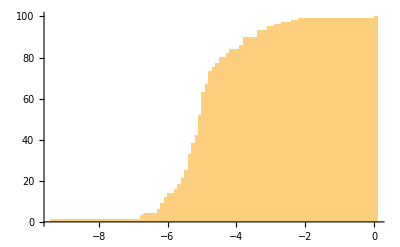

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-10.3149,0)(-9.31491,1)(-6.72018,2)(-6.72018,3)(-6.69434,4)(-6.22739,5)(-6.22739,6)(-6.14223,7)(-6.13175,8)(-6.13175,9)(-6.07994,10)(-6.06596,11)(-6.06596,12)(-5.9745,13)(-5.9745,14)(-5.76869,15)(-5.76869,16)(-5.68168,17)(-5.68168,18)(-5.55823,19)(-5.54728,20)(-5.54728,21)(-5.47956,22)(-5.47956,23)(-5.44847,24)(-5.44847,25)(-5.3591,26)(-5.3591,27)(-5.30743,28)(-5.30743,29)(-5.30339,30)(-5.30339,31)(-5.30085,32)(-5.30085,33)(-5.25251,34)(-5.25251,35)(-5.22664,36)(-5.21857,37)(-5.21857,38)(-5.19549,39)(-5.19549,40)(-5.15696,41)(-5.15696,42)(-5.09707,43)(-5.09707,44)(-5.06594,45)(-5.06594,46)(-5.05756,47)(-5.05756,48)(-5.05283,49)(-5.05283,50)(-5.01582,51)(-5.01582,52)(-4.98575,53)(-4.96812,54)(-4.96812,55)(-4.94292,56)(-4.94292,57)(-4.94053,58)(-4.94053,59)(-4.92058,60)(-4.92058,61)(-4.90983,62)(-4.90983,63)(-4.89451,64)(-4.89451,65)(-4.83475,66)(-4.83475,67)(-4.73438,68)(-4.73438,69)(-4.70402,70)(-4.70402,71)(-4.70346,72)(-4.70346,73)(-4.65477,74)(-4.65477,75)(-4.57758,76)(-4.57758,77)(-4.46215,78)(-4.46215,79)(-4.41222,80)(-4.21154,81)(-4.21154,82)(-4.12692,83)(-4.12692,84)(-3.83174,85)(-3.83174,86)(-3.78722,87)(-3.78722,88)(-3.7865,89)(-3.7865,90)(-3.36378,91)(-3.31734,92)(-3.31734,93)(-3.08773,94)(-3.08773,95)(-2.85641,96)(-2.636,97)(-2.30474,98)(-2.14537,99)(0.,100)(0.,100)

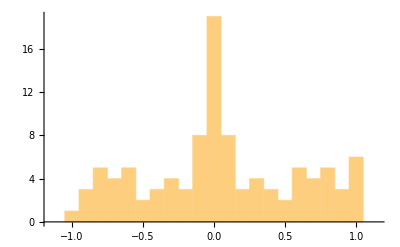

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.963706,1)(-0.934376,2)(-0.880825,3)(-0.873687,4)(-0.849024,5)(-0.831468,6)(-0.809805,7)(-0.784649,8)(-0.771521,9)(-0.739142,10)(-0.728376,11)(-0.673156,12)(-0.671802,13)(-0.645224,14)(-0.620481,15)(-0.603292,16)(-0.567454,17)(-0.566797,18)(-0.458883,19)(-0.458568,20)(-0.445453,21)(-0.440311,22)(-0.353121,23)(-0.34569,24)(-0.326803,25)(-0.29618,26)(-0.26389,27)(-0.217563,28)(-0.177011,29)(-0.17257,30)(-0.14696,31)(-0.12813,32)(-0.0996587,33)(-0.0877745,34)(-0.0651159,35)(-0.0636758,36)(-0.0629742,37)(-0.0537465,38)(-0.0434412,39)(-0.0373555,40)(-0.02987,41)(-0.0257407,42)(-0.00991909,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.00991909,53)(0.0257407,54)(0.02987,55)(0.0373555,56)(0.0434412,57)(0.0537465,58)(0.0629742,59)(0.0636758,60)(0.0651159,61)(0.0877745,62)(0.0996587,63)(0.12813,64)(0.14696,65)(0.17257,66)(0.177011,67)(0.217563,68)(0.26389,69)(0.29618,70)(0.326803,71)(0.34569,72)(0.353121,73)(0.440311,74)(0.445453,75)(0.458568,76)(0.458883,77)(0.566797,78)(0.567454,79)(0.603292,80)(0.620481,81)(0.645224,82)(0.671802,83)(0.673156,84)(0.728376,85)(0.739142,86)(0.771521,87)(0.784649,88)(0.809805,89)(0.831468,90)(0.849024,91)(0.873687,92)(0.880825,93)(0.934376,94)(0.963706,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

#### Preparations for [1, Fig.4]

```mathematica
P=Pen;
```

```mathematica
rP=#/Max[#]&/@Pen;
```

```mathematica
Export["Pen100.txt",StringRiffle[Table["\\put(0,"<>ToString[50-0.5*(i-1)]<>"){"<>StringJoin[Table[prep=ToExpression[ToString[TempRGB[rP_⟦i,j⟧]]];("\\pxl{"<>ToString[prep_⟦1⟧]<>"}{"<>ToString[prep_⟦2⟧]<>"}{"<>ToString[prep_⟦3⟧]<>"}"),{j,1,100}]]<>"}",{i,1,100}],"\n"]]
```

Pen100.txt

```mathematica
v=Eigenvectors[Transpose[P],1];
```

```mathematica
u=Reverse[Sort[Total[Transpose[#_⟦1⟧]_⟦2⟧]&/@Take[NonStopClustersEnglish,100]]]
```

{786,657,611,418,394,389,376,343,335,333,323,311,307,295,292,291,290,268,266,260,221,202,201,199,194,189,188,185,184,183,183,180,178,173,173,172,171,168,167,166,163,161,152,148,147,145,145,143,139,138,137,135,135,135,135,133,132,127,126,121,120,120,120,114,111,111,110,108,108,107,107,107,105,104,103,101,99,97,97,96,96,96,95,95,95,95,94,94,92,92,91,91,90,90,90,89,88,88,87,86}

```mathematica
prep=N[u/Total[u]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0436715)(2,0.0365041)(3,0.0339482)(4,0.0232248)(5,0.0218913)(6,0.0216135)(7,0.0208912)(8,0.0190577)(9,0.0186132)(10,0.0185021)(11,0.0179464)(12,0.0172797)(13,0.0170575)(14,0.0163907)(15,0.016224)(16,0.0161685)(17,0.0161129)(18,0.0148905)(19,0.0147794)(20,0.014446)(21,0.0122791)(22,0.0112235)(23,0.0111679)(24,0.0110568)(25,0.010779)(26,0.0105012)(27,0.0104456)(28,0.0102789)(29,0.0102234)(30,0.0101678)(31,0.0101678)(32,0.0100011)(33,0.00988999)(34,0.00961218)(35,0.00961218)(36,0.00955662)(37,0.00950106)(38,0.00933437)(39,0.00927881)(40,0.00922325)(41,0.00905656)(42,0.00894544)(43,0.00844538)(44,0.00822314)(45,0.00816757)(46,0.00805645)(47,0.00805645)(48,0.00794533)(49,0.00772308)(50,0.00766752)(51,0.00761196)(52,0.00750083)(53,0.00750083)(54,0.00750083)(55,0.00750083)(56,0.00738971)(57,0.00733415)(58,0.00705634)(59,0.00700078)(60,0.00672297)(61,0.00666741)(62,0.00666741)(63,0.00666741)(64,0.00633404)(65,0.00616735)(66,0.00616735)(67,0.00611179)(68,0.00600067)(69,0.00600067)(70,0.00594511)(71,0.00594511)(72,0.00594511)(73,0.00583398)(74,0.00577842)(75,0.00572286)(76,0.00561173)(77,0.00550061)(78,0.00538949)(79,0.00538949)(80,0.00533393)(81,0.00533393)(82,0.00533393)(83,0.00527836)(84,0.00527836)(85,0.00527836)(86,0.00527836)(87,0.0052228)(88,0.0052228)(89,0.00511168)(90,0.00511168)(91,0.00505612)(92,0.00505612)(93,0.00500056)(94,0.00500056)(95,0.00500056)(96,0.00494499)(97,0.00488943)(98,0.00488943)(99,0.00483387)(100,0.00477831)

```mathematica
prep=N[v_⟦1⟧/Total[v_⟦1⟧]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0427389)(2,0.0359008)(3,0.0344001)(4,0.0221444)(5,0.022023)(6,0.0212791)(7,0.0204973)(8,0.0197514)(9,0.0184413)(10,0.0187661)(11,0.0178566)(12,0.018584)(13,0.0177159)(14,0.0163394)(15,0.0170405)(16,0.016624)(17,0.0171587)(18,0.0138322)(19,0.0140903)(20,0.0153116)(21,0.0124126)(22,0.0109179)(23,0.0109114)(24,0.0112449)(25,0.0100791)(26,0.0101974)(27,0.0105117)(28,0.00983183)(29,0.0103186)(30,0.0102994)(31,0.0101538)(32,0.0102869)(33,0.00976647)(34,0.00979467)(35,0.00970741)(36,0.0102884)(37,0.00980244)(38,0.0090958)(39,0.00933501)(40,0.00872154)(41,0.00895465)(42,0.00912224)(43,0.00810448)(44,0.00800427)(45,0.00801203)(46,0.00777738)(47,0.00777499)(48,0.00743566)(49,0.00740558)(50,0.00739149)(51,0.00791287)(52,0.00805627)(53,0.00741824)(54,0.00703035)(55,0.00746581)(56,0.00738316)(57,0.00750157)(58,0.00725784)(59,0.00715617)(60,0.00643343)(61,0.00642784)(62,0.00689155)(63,0.00690134)(64,0.00611962)(65,0.00605191)(66,0.00617141)(67,0.00611567)(68,0.00574181)(69,0.00604926)(70,0.00599867)(71,0.00579992)(72,0.00653284)(73,0.00588162)(74,0.00555333)(75,0.00592227)(76,0.00562398)(77,0.00563289)(78,0.00551366)(79,0.00509879)(80,0.00547086)(81,0.00600555)(82,0.00538203)(83,0.00572786)(84,0.00536029)(85,0.00558624)(86,0.0054355)(87,0.00505704)(88,0.00513195)(89,0.00488509)(90,0.00509179)(91,0.00484907)(92,0.00526941)(93,0.00493628)(94,0.00488082)(95,0.0048342)(96,0.00500886)(97,0.00450342)(98,0.00514741)(99,0.00472459)(100,0.00491212)

```mathematica
1/Total[v_⟦1⟧] Sum[v_⟦1,i⟧*P_⟦i,j⟧,{i,1,N0},{j,1,N0}]
```

1.

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[AccountingForm[#_⟦2⟧]]<>")"&/@Table[M=MatrixPower[P,k];{k,1/2 Sum[Abs[1/Total[v_⟦1⟧] v_⟦1,i⟧*M_⟦i,j⟧-1/Total[v_⟦1⟧] v_⟦1,j⟧*M_⟦j,i⟧],{i,1,N0},{j,1,N0}]},{k,1,5}]]
```

(1,0.06913267664134)(2,0.00375515679879)(3,0.00035066203122)(4,0.0000372023656)(5,0.0000041419551)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

237

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersEnglish=TopicClusters;
```

```mathematica
Timing[PenTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{148.328,Null}

```mathematica
Timing[PenT=Table[v=Table[prepP=PenTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PenT];]
```

{1.29688,Null}

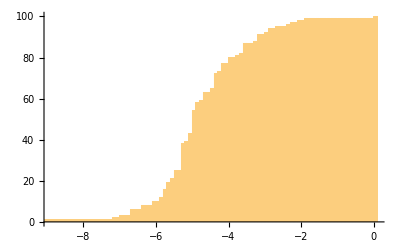

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-12.3811,0)(-11.3811,1)(-7.15148,2)(-6.98248,3)(-6.68468,4)(-6.68468,5)(-6.61223,6)(-6.38167,7)(-6.30675,8)(-6.00883,9)(-6.00883,10)(-5.80201,11)(-5.80201,12)(-5.72665,13)(-5.72665,14)(-5.70843,15)(-5.70843,16)(-5.6906,17)(-5.6906,18)(-5.65853,19)(-5.50741,20)(-5.50741,21)(-5.49354,22)(-5.49354,23)(-5.44005,24)(-5.44005,25)(-5.29904,26)(-5.29904,27)(-5.28422,28)(-5.28422,29)(-5.28311,30)(-5.28272,31)(-5.28272,32)(-5.28007,33)(-5.28007,34)(-5.27481,35)(-5.27481,36)(-5.26014,37)(-5.26014,38)(-5.1092,39)(-5.06829,40)(-5.06829,41)(-5.00688,42)(-5.00688,43)(-4.99476,44)(-4.99476,45)(-4.97087,46)(-4.97087,47)(-4.97072,48)(-4.93523,49)(-4.93523,50)(-4.92107,51)(-4.92107,52)(-4.90228,53)(-4.90228,54)(-4.86938,55)(-4.86938,56)(-4.84488,57)(-4.84488,58)(-4.77547,59)(-4.65327,60)(-4.65327,61)(-4.62329,62)(-4.62329,63)(-4.47952,64)(-4.47952,65)(-4.39712,66)(-4.39712,67)(-4.37285,68)(-4.37285,69)(-4.36746,70)(-4.36325,71)(-4.36325,72)(-4.27599,73)(-4.1296,74)(-4.1296,75)(-4.11568,76)(-4.11568,77)(-3.97565,78)(-3.95662,79)(-3.95662,80)(-3.78844,81)(-3.68951,82)(-3.57496,83)(-3.57496,84)(-3.56066,85)(-3.56066,86)(-3.51031,87)(-3.24128,88)(-3.18099,89)(-3.1658,90)(-3.1658,91)(-2.97968,92)(-2.88424,93)(-2.88424,94)(-2.65427,95)(-2.37379,96)(-2.29247,97)(-2.01032,98)(-1.80028,99)(0.,100)(0.,100)

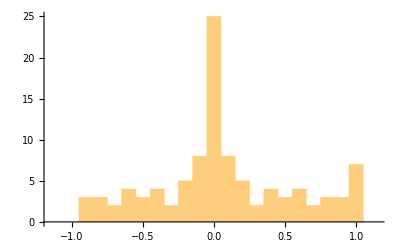

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.921508,1)(-0.913896,2)(-0.906952,3)(-0.815939,4)(-0.811287,5)(-0.795418,6)(-0.740117,7)(-0.711314,8)(-0.64081,9)(-0.634308,10)(-0.576412,11)(-0.56925,12)(-0.502514,13)(-0.489732,14)(-0.473752,15)(-0.431279,16)(-0.421645,17)(-0.39475,18)(-0.356638,19)(-0.318204,20)(-0.280477,21)(-0.24355,22)(-0.230546,23)(-0.208897,24)(-0.200848,25)(-0.196888,26)(-0.148714,27)(-0.143105,28)(-0.108566,29)(-0.0781944,30)(-0.0771544,31)(-0.071655,32)(-0.0699603,33)(-0.0662669,34)(-0.048429,35)(-0.0407977,36)(-0.0286252,37)(0.,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.0286252,57)(0.0407977,58)(0.048429,59)(0.0662669,60)(0.0699603,61)(0.071655,62)(0.0771544,63)(0.0781944,64)(0.108566,65)(0.143105,66)(0.148714,67)(0.196888,68)(0.200848,69)(0.208897,70)(0.230546,71)(0.24355,72)(0.280477,73)(0.318204,74)(0.356638,75)(0.39475,76)(0.421645,77)(0.431279,78)(0.473752,79)(0.489732,80)(0.502514,81)(0.56925,82)(0.576412,83)(0.634308,84)(0.64081,85)(0.711314,86)(0.740117,87)(0.795418,88)(0.811287,89)(0.815939,90)(0.906952,91)(0.913896,92)(0.921508,93)(1.,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Preparations for [1, Fig. 5b]

```mathematica
SelectedTopics=Cases[TopicClustersEnglish,{{___,{#,_},___},___}]_⟦1⟧&/@TopicsNamesEnglish;
```

```mathematica
KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@SelectedTopics]
```

Here are the lists of eigenvalues for the three selected topics:

```mathematica
EnglishKinQ0=KinQ0
```

{{0.96684429680455,0.15826962277985,0.12814810055663,0.10527846971632,0.065256166694679,0.049531282426573,0.039045757245365,0.036168507501952,0.036168507501952,0.030764539917496,0.030764539917496,0.026544101806293,0.026544101806293,0.018666360370293,0.018297510034573,0.013631540154267,0.013631540154267,0.010905388997874,0.010905388997874,0.0093877700317952,0.0093877700317952,0.0088145548947543,0.0076038665069392,0.0076038665069392,0},{0.89865749117438,0.096151626412867,0.080329772295716,0.075715148414852,0.061104284898873,0.038856817013835,0.038856817013835,0.027836196087545,0.027836196087545,0.022866057395476,0.019310317182122,0.018434309595855,0.018434309595855,0.018196483507101,0.018196483507101,0.017873937290036,0.013490934815024,0.013490934815024,0.012600606784418,0.0086953051273753,0.0086953051273753,0.0083741800256109,0.0083741800256109,0.0082170469825677,0.0082170469825677,0.0076141449539015,0.0076141449539015,0.0061028870804117,0.0060788718506522,0.0060788718506522,0.0058408146566645,0.0043465308075192,0.0042584793409954,0.0042584793409954,0.0033420947402719,0.0012421532717559,0},{0.72454750286994,0.20830029603277,0.12829335894057,0.072867255441827,0.061948942954887,0.061948942954887,0.044286535037415,0.044286535037415,0.038390198990604,0.035001124002286,0.023196661110345,0.023196661110345,0.018187217133985,0.018187217133985,0.015663659644382,0.015663659644382,0.014345020311608,0.014345020311608,0.011336865645403,0.011336865645403,0.010714288085327,0.010579397074542,0.010579397074542,0.0050705807890795,0.0042603826175243,0.00060260662072419,0}}

```mathematica
EnglishKinQ=KinQ
```

{{0.96684429680455,0.15826962277985,0.12814810055663,0.10527846971632,0.065256166694679,0.049531282426573,0.039045757245365,0.036168507501952,0.036168507501952,0.030764539917496,0.030764539917496,0.026544101806293,0.026544101806293,0.018666360370293,0.018297510034573},{0.89865749117438,0.096151626412867,0.080329772295716,0.075715148414852,0.061104284898873,0.038856817013835,0.038856817013835,0.027836196087545,0.027836196087545,0.022866057395476,0.019310317182122,0.018434309595855,0.018434309595855,0.018196483507101,0.018196483507101,0.017873937290036,0.013490934815024,0.013490934815024,0.012600606784418,0.0086953051273753,0.0086953051273753},{0.72454750286994,0.20830029603277,0.12829335894057,0.072867255441827,0.061948942954887,0.061948942954887,0.044286535037415,0.044286535037415,0.038390198990604,0.035001124002286,0.023196661110345,0.023196661110345,0.018187217133985,0.018187217133985}}

```mathematica
TopicNames=TopicsNamesEnglish
```

{pride,Darcy,Elizabeth}

```mathematica
Cl=TopicClustersEnglish;
```

```mathematica
PT=PenTopic;
```

```mathematica
AffinitySmallWorlds=Table[PT_⟦SeekPos[TopicNames_⟦k⟧,Cl],TopicSmallWorlds_⟦k,j⟧,3⟧,{k,1,Length[TopicNames]},{j,1,Length[TopicSmallWorlds_⟦k⟧]}];
```

```mathematica
SmallWorldWeights=Table[v=Eigenvectors[Transpose[RenormPSW_⟦k⟧],1];prob=v_⟦1⟧/Total[v_⟦1⟧];Table[ReplacePart[Cl_⟦TopicSmallWorlds_⟦k,m⟧⟧,{2->prob_⟦m⟧,5->AffinitySmallWorlds_⟦k,m⟧}],{m,1,Length[RenormPSW_⟦k⟧]}],{k,1,Length[RenormPSW]}];
```

```mathematica
SortWordClusters[list_,ScalingFactor_,MaxClusters_]:=(AllCluster=Take[Sort[(prep=CensorCluster[#_⟦1⟧];{prep,#_⟦2⟧,Total[Transpose[prep]_⟦2⟧],#_⟦4⟧,#_⟦5⟧})&/@list,#1[[2]]>#2[[2]]&],UpTo[MaxClusters]];SizedWords=Table[Width=Total[Max/@StringLength[#_⟦2⟧&/@#&/@SplitEven[EvenOut[Transpose[AllCluster_⟦n,1⟧]]]]];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦1⟧,40,Length[SmallWorldWeights_⟦1⟧]];SmallWorldCloudPlot[1,20,"en-pride.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦2⟧,40,Length[SmallWorldWeights_⟦2⟧]];SmallWorldCloudPlot[1,25,"en-Darcy.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦3⟧,40,Length[SmallWorldWeights_⟦3⟧]];SmallWorldCloudPlot[1,25,"en-Eliza.txt"];
```